```mathematica
Exit[]
```

```mathematica
$Assumptions={_∈Reals, X0[x]∈Reals,Y0[x]∈Reals,aa>0,κ>0,β>0,Δ>0,lp>0,ϵ>0,Q1>0, μ>0,μ1>0,μ2>0,μ3>0,Δ>0,η>0,Px[x1]>0,Py[x1]>0,Sin[θ]>0};
```

## Continuum Hamiltonian

### Derive spherical symmetric Ashtekar variables

```mathematica
$Assumptions={_∈Reals, X0[x]∈Reals,Y0[x]∈Reals,Eϕ[x]∈Reals,Ex[x]∈Reals,aa>0,κ>0,β>0,lp>0,ϵ>0,λ[1]>0,λ[2]>0,λ[3]>0,Q1>0, μ>0,μ1>0,μ2>0,μ3>0,Δ>0,η>0,py[ρ]∈Reals,px[ρ]∈Reals,-3 K0[t]^2+Λ P0[t]<0,P0[t]>0,Sin[θ]>0};
```

```mathematica
xx={ρ,θ,ϕ};
```

```mathematica
A={{β x[ρ],0,Cos[θ]},{0,β y[ρ],-(Sin[θ] px'[ρ])/py[ρ]},{0,px'[ρ]/py[ρ],β Sin[θ] y[ρ]}};
EE2={{px[ρ]Sin[θ],0,0},{0,py[ρ]/2 Sin[θ],0},{0,0,py[ρ]/2}};
```

```mathematica
EE2inv=Inverse[EE2]//FullSimplify
```

{{Csc[θ]/px[ρ],0,0},{0,(2 Csc[θ])/py[ρ],0},{0,0,2/py[ρ]}}

```mathematica
detE2=Det[EE2]
```

1/4 px[ρ] py[ρ]^2 Sin[θ]^2

```mathematica
triad2=EE2/√Abs[detE2]
```

{{(2 px[ρ] Sin[θ])/(√Abs[px[ρ] py[ρ]^2 Sin[θ]^2]),0,0},{0,(py[ρ] Sin[θ])/(√Abs[px[ρ] py[ρ]^2 Sin[θ]^2]),0},{0,0,py[ρ]/(√Abs[px[ρ] py[ρ]^2 Sin[θ]^2])}}

```mathematica
cotriad2=((Inverse[triad2]//FullSimplify))
```

{{(√Abs[px[ρ]] Abs[py[ρ]])/(2 px[ρ]),0,0},{0,(√Abs[px[ρ]] Abs[py[ρ]])/py[ρ],0},{0,0,(√Abs[px[ρ]] Abs[py[ρ]] Sin[θ])/py[ρ]}}

```mathematica
q2=ParallelTable[∑_(i=1)^3 (cotriad2[[i,a]]//FullSimplify)(cotriad2[[i,b]]//FullSimplify),{a,1,3},{b,1,3}]//FullSimplify
```

{{py[ρ]^2/(4 Abs[px[ρ]]),0,0},{0,Abs[px[ρ]],0},{0,0,Abs[px[ρ]] Sin[θ]^2}}

```mathematica
q2inv=Inverse[q2]//FullSimplify
detq2=Det[q2]//FullSimplify
```

{{(4 Abs[px[ρ]])/py[ρ]^2,0,0},{0,1/Abs[px[ρ]],0},{0,0,Csc[θ]^2/Abs[px[ρ]]}}

1/4 Abs[px[ρ]] py[ρ]^2 Sin[θ]^2

```mathematica
Christ2=ParallelTable[∑_(α=1)^3 1/2 q2inv[[σ,α]](D[q2[[α,μ]], xx[[ν]]]+D[q2[[α,ν]], xx[[μ]]]-D[q2[[μ,ν]], xx[[α]]])//FullSimplify,{σ,1,3},{μ,1,3},{ν,1,3}];gamma2=ParallelTable[-∑_(b=1)^3 triad2[[b,k]](D[cotriad2[[j,b]], xx[[a]]]-∑_(c=1)^3 Christ2[[c,a,b]]cotriad2[[j,c]])//FullSimplify,{a,1,3},{j,1,3},{k,1,3}];
Γ2=ParallelTable[-1/2∑_(j=1)^3 ∑_(k=1)^3 LeviCivitaTensor[3][[i,j,k]]gamma2[[a,j,k]]//FullSimplify,{i,1,3},{a,1,3}]//FullSimplify;
KK=ParallelTable[(A[[i,j]]-Γ2[[i,j]])/β//FullSimplify,{i,1,3},{j,1,3}];
```

```mathematica
ParallelTable[∑_(a=1)^3 (D[EE2[[a,j]], xx[[a]]]+∑_(k=1)^3 (gamma2[[a,j,k]]EE2[[a,k]])),{j,1,3}]//FullSimplify
```

{Piecewise[{{ComplexInfinity, py[ρ]==0}, {0, True}}],0,0}

```mathematica
Rform2=ParallelTable[Series[(D[(Γ2[[j,b]]), xx[[a]]]-D[(Γ2[[j,a]]), xx[[b]]]+∑_(k=1)^3 ∑_(l=1)^3 LeviCivitaTensor[3][[j,k,l]](Γ2[[k,a]])(Γ2[[l,b]])),{ϵ,0,2}]//Simplify,{j,1,3},{a,1,3},{b,1,3}];
ParallelTable[Series[∑_(j=1)^3 ∑_(b=1)^3 (Rform2[[j,a,b]])EE2[[b,j]],{ϵ,0,2}]//Simplify,{a,1,3}]
```

{0,0,0}

```mathematica
F=ParallelTable[Series[D[(A[[j,b]]//Normal), xx[[a]]]-D[(A[[j,a]]//Normal), xx[[b]]]+∑_(k=1)^3 ∑_(l=1)^3 LeviCivitaTensor[3][[j,k,l]](A[[k,a]]//Normal)(A[[l,b]]//Normal),{ϵ,0,2}]//FullSimplify,{j,1,3},{a,1,3},{b,1,3}];
F1=ParallelTable[Rform2[[j,a,b]]+β(D[KK[[j,b]], xx[[a]]]+∑_(k=1)^3 ∑_(l=1)^3 LeviCivitaTensor[3][[j,k,l]]Γ2[[k,a]]KK[[l,b]])-β(D[KK[[j,a]], xx[[b]]]+∑_(k=1)^3 ∑_(l=1)^3 LeviCivitaTensor[3][[j,k,l]]Γ2[[k,b]]KK[[l,a]])+β^2∑_(k=1)^3 ∑_(l=1)^3 LeviCivitaTensor[3][[j,k,l]]KK[[k,a]]KK[[l,b]]//Simplify,{j,1,3},{a,1,3},{b,1,3}];
F-F1//Simplify
```

{{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}}}

```mathematica
F[[2,1,2]]
```

β (-(x[ρ] px'[ρ])/py[ρ]+y'[ρ])

```mathematica
HamEuc=FullSimplify[1/κ(∑_(a=1)^3 ∑_(b=1)^3 ∑_(j=1)^3 ∑_(k=1)^3 ∑_(l=1)^3 LeviCivitaTensor[3][[j,k,l]]F[[j,a,b]] ((EE2[[a,k]])(EE2[[b,l]]))/(√detq2)+2Λ √detq2)/.Λ->0,Assumptions-> Sin[θ]>0]
```

(Sin[θ] (4 β^2 px[ρ] py[ρ]^2 x[ρ] y[ρ]+py[ρ]^3 (-1+β^2 y[ρ]^2)-4 px[ρ] px'[ρ] py'[ρ]+py[ρ] (px'[ρ]^2+4 px[ρ] px''[ρ])))/(κ √Abs[px[ρ]] py[ρ] √(py[ρ]^2))

```mathematica
HamEuc*(κ √Abs[px[ρ] ])/(Sign[py[ρ]]Sin[θ])//FullSimplify//Expand
```

-py[ρ]+4 β^2 px[ρ] x[ρ] y[ρ]+β^2 py[ρ] y[ρ]^2+px'[ρ]^2/py[ρ]-(4 px[ρ] px'[ρ] py'[ρ])/py[ρ]^2+(4 px[ρ] px''[ρ])/py[ρ]

```mathematica
HamLor=-1/κ(β^2+1)∑_(a=1)^3 ∑_(b=1)^3 ∑_(k=1)^3 ∑_(l=1)^3 ((KK[[k,a]])(KK[[l,b]])-(KK[[l,a]])(KK[[k,b]]))((EE2[[a,k]])(EE2[[b,l]]))/(√detq2)//FullSimplify
```

-((1+β^2) py[ρ] Sin[θ] y[ρ] (4 px[ρ] x[ρ]+py[ρ] y[ρ]))/(κ √Abs[px[ρ]] Abs[py[ρ]])

```mathematica
ScalarH=HamEuc+HamLor//FullSimplify
```

-(Abs[py[ρ]] Sin[θ] (4 px[ρ] py[ρ]^2 x[ρ] y[ρ]+py[ρ]^3 (1+y[ρ]^2)+4 px[ρ] px'[ρ] py'[ρ]-py[ρ] (px'[ρ]^2+4 px[ρ] px''[ρ])))/(κ √Abs[px[ρ]] py[ρ]^3)

```mathematica
FullSimplify[ScalarH*(κ √Abs[px[ρ] ])/(Sign[py[ρ]]Sin[θ])]/.Sign[px[ρ]]^4->1//FullSimplify
```

-4 px[ρ] x[ρ] y[ρ]-py[ρ] (1+y[ρ]^2)-(4 px[ρ] px'[ρ] py'[ρ])/py[ρ]^2+(px'[ρ]^2+4 px[ρ] px''[ρ])/py[ρ]

```mathematica
Det[EE2]
```

1/4 px[ρ] py[ρ]^2 Sin[θ]^2

```mathematica
Det[EE2]/.pullin
```

Ex[ρ] Eϕ[ρ]^2 Sin[θ]^2

```mathematica
DiffAE=ParallelTable[2/(κ β)∑_(b=1)^3 ∑_(j=1)^3 F[[j,a,b]]EE2[[b,j]]//FullSimplify,{a,1,3}]
Diff=ParallelTable[FullSimplify[(2 ∑_(a=1)^3 DiffAE[[a]]EE2[[a,j]])/(√detq2)],{j,1,3}]//Normal
```

{(2 Sin[θ] (-x[ρ] px'[ρ]+py[ρ] y'[ρ]))/κ,0,0}

{(8 px[ρ] Sin[θ]^2 (-x[ρ] px'[ρ]+py[ρ] y'[ρ]))/(κ √Abs[px[ρ]] √(py[ρ]^2 Sin[θ]^2)),0,0}

```mathematica
(DiffAE/.pullin)
```

{(2 Sin[θ] (-2 Kx[ρ] Ex'[ρ]+2 Eϕ[ρ] Kϕ'[ρ]))/κ,0,0}

```mathematica
2π∫_0^π (DiffAE/.pullin)ⅆθ
```

{(16 π (-Kx[ρ] Ex'[ρ]+Eϕ[ρ] Kϕ'[ρ]))/κ,0,0}

```mathematica
Hbk=(√(ScalarH^2-1/4∑_(j=1)^3 Diff[[j]]Diff[[j]])//FullSimplify)/.Sign[px[ρ]]^4->1//FullSimplify
```

1/(κ √Abs[px[ρ]] Abs[py[ρ]]^3)Sin[θ] √(-16 px[ρ]^2 py[ρ]^4 (x[ρ] px'[ρ]-py[ρ] y'[ρ])^2+py[ρ]^2 (4 px[ρ] py[ρ]^2 x[ρ] y[ρ]+py[ρ]^3 (1+y[ρ]^2)+4 px[ρ] px'[ρ] py'[ρ]-py[ρ] (px'[ρ]^2+4 px[ρ] px''[ρ]))^2)

```mathematica
∫_0^π Sin[x]ⅆx
```

2

```mathematica
(((2π∫_0^π ScalarHⅆθ/.Sign[px[ρ]]^4->1//FullSimplify)//Expand)/.pullin)*κ/(4π)*(√Abs[Ex[ρ]])/Sign[Eϕ[ρ]]//FullSimplify
```

-8 Ex[ρ] Kx[ρ] Kϕ[ρ]-2 Eϕ[ρ] (1+Kϕ[ρ]^2)-(2 Ex[ρ] Ex'[ρ] Eϕ'[ρ])/Eϕ[ρ]^2+(Ex'[ρ]^2+4 Ex[ρ] Ex''[ρ])/(2 Eϕ[ρ])

```mathematica
pullin={px[ρ]->Ex[ρ],py[ρ]->2 Eϕ[ρ], x[ρ]-> 2Kx[ρ],y[ρ]-> Kϕ[ρ],y'[ρ]-> Kϕ'[ρ],px'[ρ]->Ex'[ρ],py'[ρ]->2 Eϕ'[ρ],px''[ρ]->Ex''[ρ]};
```

```mathematica
Hgauss0=((2π∫_0^π ScalarHⅆθ/.Sign[px[ρ]]^4->1//FullSimplify)//Expand)
```

-(4 π Abs[py[ρ]])/(κ √Abs[px[ρ]])-(16 π Abs[py[ρ]] px[ρ] x[ρ] y[ρ])/(κ √Abs[px[ρ]] py[ρ])-(4 π Abs[py[ρ]] y[ρ]^2)/(κ √Abs[px[ρ]])+(4 π Abs[py[ρ]] px'[ρ]^2)/(κ √Abs[px[ρ]] py[ρ]^2)-(16 π Abs[py[ρ]] px[ρ] px'[ρ] py'[ρ])/(κ √Abs[px[ρ]] py[ρ]^3)+(16 π Abs[py[ρ]] px[ρ] px''[ρ])/(κ √Abs[px[ρ]] py[ρ]^2)

```mathematica
Hgauss=((2π∫_0^π ScalarHⅆθ/.Sign[px[ρ]]^4->1//FullSimplify)//Expand)/.{(16 π Abs[py[ρ]] px[ρ] px''[ρ])/(κ √Abs[px[ρ]] py[ρ]^2)->- D[((16 π Abs[py[ρ]] px[ρ])/(κ √Abs[px[ρ]] py[ρ]^2)), ρ]px'[ρ]}//FullSimplify
```

-(4 π Abs[py[ρ]] (4 px[ρ] py[ρ] x[ρ] y[ρ]+py[ρ]^2 (1+y[ρ]^2)+px'[ρ]^2))/(κ √Abs[px[ρ]] py[ρ]^2)

```mathematica
Hgauss*(κ √Abs[px[ρ]])/(-4π Sign[py[ρ]])//FullSimplify
```

4 px[ρ] x[ρ] y[ρ]+py[ρ] (1+y[ρ]^2)+px'[ρ]^2/py[ρ]

```mathematica
Hgauss//Expand
```

-(4 π Abs[py[ρ]])/(κ √Abs[px[ρ]])-(16 π Abs[py[ρ]] px[ρ] x[ρ] y[ρ])/(κ √Abs[px[ρ]] py[ρ])-(4 π Abs[py[ρ]] y[ρ]^2)/(κ √Abs[px[ρ]])-(4 π Abs[py[ρ]] px'[ρ]^2)/(κ √Abs[px[ρ]] py[ρ]^2)

```mathematica
(D[Hgauss, px[ρ]]) δpx[ρ]-D[(D[Hgauss1, px'[ρ]]), ρ] δpx[ρ]+D[((D[Hgauss1, px'[ρ]]) δpx[ρ]), ρ]//FullSimplify
```

(2 π Abs[py[ρ]] δpx[ρ] (-4 Abs[px[ρ]] py[ρ] x[ρ] y[ρ]+py[ρ]^2 Sign[px[ρ]] (1+y[ρ]^2)+Sign[px[ρ]] px'[ρ]^2))/(κ Abs[px[ρ]]^(3/2) py[ρ]^2)

```mathematica
((D[Hgauss, px'[ρ]]) δpx[ρ])//FullSimplify
```

-(8 π δpx[ρ] px'[ρ])/(κ √Abs[px[ρ]] Abs[py[ρ]])

```mathematica
Cpullin=Refine[(Hgauss0/.pullin)//FullSimplify//Expand]/.ρ->x
```

-(8 π Abs[Eϕ[x]])/(κ √Abs[Ex[x]])-(32 π Abs[Eϕ[x]] Ex[x] Kx[x] Kϕ[x])/(κ √Abs[Ex[x]] Eϕ[x])-(8 π Abs[Eϕ[x]] Kϕ[x]^2)/(κ √Abs[Ex[x]])+(2 π Abs[Eϕ[x]] Ex'[x]^2)/(κ √Abs[Ex[x]] Eϕ[x]^2)-(8 π Abs[Eϕ[x]] Ex[x] Ex'[x] Eϕ'[x])/(κ √Abs[Ex[x]] Eϕ[x]^3)+(8 π Abs[Eϕ[x]] Ex[x] Ex''[x])/(κ √Abs[Ex[x]] Eϕ[x]^2)

```mathematica
pullin
```

{px[ρ]→Ex[ρ],py[ρ]→2 Eϕ[ρ],x[ρ]→2 Kx[ρ],y[ρ]→Kϕ[ρ],y'[ρ]→Kϕ'[ρ],px'[ρ]→Ex'[ρ],py'[ρ]→2 Eϕ'[ρ],px''[ρ]→Ex''[ρ]}

### Gambini-Pullin Hamiltonian

```mathematica
Cpullin=-((8 π Abs[Eϕ[x]])/(κ √Abs[Ex[x]]))-(32 π Abs[Eϕ[x]] Ex[x] Kx[x] Kϕ[x])/(κ √Abs[Ex[x]] Eϕ[x])-(8 π Abs[Eϕ[x]] Kϕ[x]^2)/(κ √Abs[Ex[x]])+(2 π Abs[Eϕ[x]] Ex'[x]^2)/(κ √Abs[Ex[x]] Eϕ[x]^2)-(8 π Abs[Eϕ[x]] Ex[x] Ex'[x] Eϕ'[x])/(κ √Abs[Ex[x]] Eϕ[x]^3)+(8 π Abs[Eϕ[x]] Ex[x] Ex''[x])/(κ √Abs[Ex[x]] Eϕ[x]^2)
```

-(8 π Abs[Eϕ[x]])/(κ √Abs[Ex[x]])-(32 π Abs[Eϕ[x]] Ex[x] Kx[x] Kϕ[x])/(κ √Abs[Ex[x]] Eϕ[x])-(8 π Abs[Eϕ[x]] Kϕ[x]^2)/(κ √Abs[Ex[x]])+(2 π Abs[Eϕ[x]] Ex'[x]^2)/(κ √Abs[Ex[x]] Eϕ[x]^2)-(8 π Abs[Eϕ[x]] Ex[x] Ex'[x] Eϕ'[x])/(κ √Abs[Ex[x]] Eϕ[x]^3)+(8 π Abs[Eϕ[x]] Ex[x] Ex''[x])/(κ √Abs[Ex[x]] Eϕ[x]^2)

```mathematica
Cpullin1=FullSimplify[(Cpullin/.(8 π Abs[Eϕ[x]] Ex[x] Ex''[x])/(κ √Abs[Ex[x]] Eϕ[x]^2)-> -D[((8 π Abs[Eϕ[x]] Ex[x])/(κ √Abs[Ex[x]] Eϕ[x]^2)), x] Ex'[x]//FullSimplify),Assumptions->{Eϕ[x]∈Reals,Ex[x]∈Reals}]
boundary1=(8 π Abs[Eϕ[x]] Ex[x])/(κ √Abs[Ex[x]] Eϕ[x]^2) Ex'[x]
```

-(2 π (4 Eϕ[x] (4 Ex[x] Kx[x] Kϕ[x]+Eϕ[x] (1+Kϕ[x]^2))+Ex'[x]^2))/(κ √Abs[Ex[x]] Abs[Eϕ[x]])

(8 π Abs[Eϕ[x]] Ex[x] Ex'[x])/(κ √Abs[Ex[x]] Eϕ[x]^2)

```mathematica
CpullinS=Simplify[Cpullin,Assumptions->{Eϕ[x]>0,Ex[x]>0}]
Cpullin1S=Simplify[Cpullin1,Assumptions->{Eϕ[x]>0,Ex[x]>0}]
```

-(2 π (16 Ex[x] Eϕ[x]^2 Kx[x] Kϕ[x]+4 Eϕ[x]^3 (1+Kϕ[x]^2)+4 Ex[x] Ex'[x] Eϕ'[x]-Eϕ[x] (Ex'[x]^2+4 Ex[x] Ex''[x])))/(κ √Ex[x] Eϕ[x]^2)

-(2 π (16 Ex[x] Eϕ[x] Kx[x] Kϕ[x]+4 Eϕ[x]^2 (1+Kϕ[x]^2)+Ex'[x]^2))/(κ √Ex[x] Eϕ[x])

```mathematica
eomEx1=FullSimplify[(D[CpullinS, Ex[x]])δEx[x]-D[(D[CpullinS, Ex'[x]]), x]δEx[x]+D[D[(D[CpullinS, Ex''[x]]), x], x]δEx[x]]
boundaryEx1=(D[Cpullin, Ex'[x]])δEx[x]+(D[Cpullin, Ex''[x]])δEx'[x]-D[(D[Cpullin, Ex''[x]]), x]δEx[x]//FullSimplify
```

(π δEx[x] (-16 Ex[x] Eϕ[x]^2 Kx[x] Kϕ[x]+4 Eϕ[x]^3 (1+Kϕ[x]^2)-4 Ex[x] Ex'[x] Eϕ'[x]-Eϕ[x] (Ex'[x]^2-4 Ex[x] Ex''[x])))/(κ Ex[x]^(3/2) Eϕ[x]^2)

1/(κ Abs[Ex[x]]^(3/2) Eϕ[x]^3)(4 π δEx[x] (Abs[Eϕ[x]] Eϕ[x] (-Abs[Ex[x]]+Ex[x] Abs'[Ex[x]]) Ex'[x]+2 Abs[Ex[x]] Ex[x] (Abs[Eϕ[x]]-Eϕ[x] Abs'[Eϕ[x]]) Eϕ'[x])+8 π Abs[Ex[x]] Abs[Eϕ[x]] Ex[x] Eϕ[x] δEx'[x])

```mathematica
eomEx10=(D[Cpullin1S, Ex[x]])δEx[x]-D[(D[Cpullin1S, Ex'[x]]), x]δEx[x]//FullSimplify
(D[Cpullin1S, Ex'[x]])δEx[x]//FullSimplify
```

(π δEx[x] (-16 Ex[x] Eϕ[x]^2 Kx[x] Kϕ[x]+4 Eϕ[x]^3 (1+Kϕ[x]^2)-4 Ex[x] Ex'[x] Eϕ'[x]-Eϕ[x] (Ex'[x]^2-4 Ex[x] Ex''[x])))/(κ Ex[x]^(3/2) Eϕ[x]^2)

-(4 π δEx[x] Ex'[x])/(κ √Ex[x] Eϕ[x])

```mathematica
eomEx1-eomEx10
```

0

```mathematica
FullSimplify[D[(-(8 π Abs[Eϕ[x]] Ex[x] Ex'[x])/(κ √Abs[Ex[x]] Eϕ[x]^2)), Ex[x]]δEx[x],Assumptions->{Eϕ[x]∈Reals,Ex[x]∈Reals}]/.{ Sign'[Ex[x]]-> 0,Sign[Ex[x]]^2-> 1}
```

-(4 π δEx[x] Ex'[x])/(κ √Abs[Ex[x]] Abs[Eϕ[x]])

```mathematica
delta[Cpullin1S,Ex] δEx[x]-eomEx1//FullSimplify
```

δEx[x] (delta[-(2 π (4 Eϕ[x] (4 Ex[x] Kx[x] Kϕ[x]+Eϕ[x] (1+Kϕ[x]^2))+Ex'[x]^2))/(κ √Ex[x] Eϕ[x]),Ex]+(π (16 Ex[x] Eϕ[x]^2 Kx[x] Kϕ[x]-4 Eϕ[x]^3 (1+Kϕ[x]^2)+4 Ex[x] Ex'[x] Eϕ'[x]+Eϕ[x] (Ex'[x]^2-4 Ex[x] Ex''[x])))/(κ Ex[x]^(3/2) Eϕ[x]^2))

```mathematica
eomEϕ1=(D[CpullinS, Eϕ[x]])δEϕ[x]-D[(D[CpullinS, Eϕ'[x]]), x]δEϕ[x]//FullSimplify
boundaryEϕ1=(D[Cpullin, Eϕ'[x]])δEϕ[x]//FullSimplify
```

(2 π δEϕ[x] (-4 Eϕ[x]^2 (1+Kϕ[x]^2)+Ex'[x]^2))/(κ √Ex[x] Eϕ[x]^2)

-(8 π Abs[Eϕ[x]] Ex[x] δEϕ[x] Ex'[x])/(κ √Abs[Ex[x]] Eϕ[x]^3)

```mathematica
(boundaryEx1+boundaryEϕ1)
```

-(8 π Abs[Eϕ[x]] Ex[x] δEϕ[x] Ex'[x])/(κ √Abs[Ex[x]] Eϕ[x]^3)+1/(κ Abs[Ex[x]]^(3/2) Eϕ[x]^3)(4 π δEx[x] (Abs[Eϕ[x]] Eϕ[x] (-Abs[Ex[x]]+Ex[x] Abs'[Ex[x]]) Ex'[x]+2 Abs[Ex[x]] Ex[x] (Abs[Eϕ[x]]-Eϕ[x] Abs'[Eϕ[x]]) Eϕ'[x])+8 π Abs[Ex[x]] Abs[Eϕ[x]] Ex[x] Eϕ[x] δEx'[x])

```mathematica
assumE={Eϕ[x]>0,Ex[x]>0};
boundaryterm=Refine[-(8 π Ex[x] Ex'[x])/(κ Abs[Eϕ[x]] √Abs[Ex[x]]),Assumptions->assumE];
boundaryE1=Refine[(boundaryEx1+boundaryEϕ1),Assumptions->assumE]
boundaryvari=(D[boundaryterm, Eϕ[x]])δEϕ[x]+(D[boundaryterm, Ex'[x]])δEx'[x]+(D[boundaryterm, Ex[x]])δEx[x]
boundaryreminder=FullSimplify[boundaryvari+boundaryE1,Assumptions->assumE]
```

-(8 π √Ex[x] δEϕ[x] Ex'[x])/(κ Eϕ[x]^2)+(4 π δEx[x] (Eϕ[x]^2 (-Ex[x]+Ex[x] Abs'[Ex[x]]) Ex'[x]+2 Ex[x]^2 (Eϕ[x]-Eϕ[x] Abs'[Eϕ[x]]) Eϕ'[x])+8 π Ex[x]^2 Eϕ[x]^2 δEx'[x])/(κ Ex[x]^(3/2) Eϕ[x]^3)

-(4 π δEx[x] Ex'[x])/(κ √Ex[x] Eϕ[x])+(8 π √Ex[x] δEϕ[x] Ex'[x])/(κ Eϕ[x]^2)-(8 π √Ex[x] δEx'[x])/(κ Eϕ[x])

-(4 π δEx[x] Ex'[x])/(κ √Ex[x] Eϕ[x])

```mathematica
Series[boundaryvari/.{Ex[x]->3/2 (3/2)^(1/3) (√(Rs+Rs1/x) (-t+x))^(4/3),Ex'[x]->D[(3/2 (3/2)^(1/3) (√(Rs+Rs1/x) (-t+x))^(4/3)), x],Eϕ[x]->(3/2)^(1/3) √(Rs+Rs1/x) (√(Rs+Rs1/x) (-t+x))^(1/3)},{x,∞,1}]
```

(-(8 ((2/3)^(2/3) π) (1/x)^(2/3))/(√((√Rs (√Rs x)^(1/3))/x^(1/3)) κ)+O[1/x]^(4/3)) δEx[x]+((8 2^(2/3) 3^(1/3) π x^(1/3) √((√Rs (√Rs x)^(1/3))/x^(1/3)) x^(1/3))/(√Rs (√Rs x)^(1/3) κ)-(4 ((2/3)^(2/3) π (5 Rs1+2 Rs t) x^(1/3) √((√Rs (√Rs x)^(1/3))/x^(1/3))) (1/x)^(2/3))/(Rs^(3/2) (√Rs x)^(1/3) κ)+O[1/x]^(5/3)) δEϕ[x]+(-(4 (2^(2/3) 3^(1/3) π x^(1/3) √((√Rs (√Rs x)^(1/3))/x^(1/3))) x^(1/3))/(√Rs (√Rs x)^(1/3) κ)+(4 (2/3)^(2/3) π (Rs1+Rs t) x^(1/3) √((√Rs (√Rs x)^(1/3))/x^(1/3)) (1/x)^(2/3))/(Rs^(3/2) (√Rs x)^(1/3) κ)+O[1/x]^(5/3)) δEx'[x]

```mathematica
Series[boundaryterm/.{Ex[x]->3/2 (3/2)^(1/3) (√(Rs+Rs1/x+Rs2/x^2) (-t+x))^(4/3),Ex'[x]->D[(3/2 (3/2)^(1/3) (√(Rs+Rs1/x+Rs2/x^2) (-t+x))^(4/3)), x],Eϕ[x]->(3/2)^(1/3) √(Rs+Rs1/x+Rs2/x^2) (√(Rs+Rs1/x) (-t+x))^(1/3)},{x,∞,1}]
```

-(8 (2^(1/3) 3^(2/3) π √((√Rs (√Rs x)^(1/3))/x^(1/3))) x^(2/3))/κ+(4 (2/3)^(1/3) π (Rs1+4 Rs t) √((√Rs (√Rs x)^(1/3))/x^(1/3)) (1/x)^(1/3))/(Rs κ)+O[1/x]^(4/3)

```mathematica
delta[CpullinS,Eϕ]δEϕ[x]-eomEϕ1//FullSimplify
```

δEϕ[x] (delta[-(2 π (16 Ex[x] Eϕ[x]^2 Kx[x] Kϕ[x]+4 Eϕ[x]^3 (1+Kϕ[x]^2)+4 Ex[x] Ex'[x] Eϕ'[x]-Eϕ[x] (Ex'[x]^2+4 Ex[x] Ex''[x])))/(κ √Ex[x] Eϕ[x]^2),Eϕ]-(2 π (-4 Eϕ[x]^2 (1+Kϕ[x]^2)+Ex'[x]^2))/(κ √Ex[x] Eϕ[x]^2))

```mathematica
FullSimplify[(D[CpullinS, Eϕ[x]])δEϕ[x]-D[(D[CpullinS, Eϕ'[x]]), x]δEϕ[x]+D[D[(D[CpullinS, Eϕ''[x]]), x], x]δEϕ[x]]-eomEϕ1
```

0

```mathematica
eomKx1=(D[Cpullin1S, Kx[x]])δKx[x]//FullSimplify
```

-(32 π √Ex[x] Kϕ[x] δKx[x])/κ

```mathematica
FullSimplify[(D[CpullinS, Kx[x]])δKx[x]-D[(D[CpullinS, Kx'[x]]), x]δKx[x]+D[D[(D[CpullinS, Kx''[x]]), x], x]δKx[x]]-eomKx1
```

0

```mathematica
delta[CpullinS,Kx]δKx[x]-eomKx1//FullSimplify
```

(delta[-(2 π (16 Ex[x] Eϕ[x]^2 Kx[x] Kϕ[x]+4 Eϕ[x]^3 (1+Kϕ[x]^2)+4 Ex[x] Ex'[x] Eϕ'[x]-Eϕ[x] (Ex'[x]^2+4 Ex[x] Ex''[x])))/(κ √Ex[x] Eϕ[x]^2),Kx]+(32 π √Ex[x] Kϕ[x])/κ) δKx[x]

```mathematica
eomKϕ1=(D[Cpullin1S, Kϕ[x]])δKϕ[x]//FullSimplify
```

-(16 π (2 Ex[x] Kx[x]+Eϕ[x] Kϕ[x]) δKϕ[x])/(κ √Ex[x])

```mathematica
FullSimplify[(D[CpullinS, Kϕ[x]])δKϕ[x]-D[(D[CpullinS, Kϕ'[x]]), x]δKϕ[x]+D[D[(D[CpullinS, Kϕ''[x]]), x], x]δKϕ[x]]-eomKϕ1
```

0

```mathematica
delta[CpullinS,Kϕ]δKϕ[x]-eomKϕ1//FullSimplify
```

(delta[-(2 π (16 Ex[x] Eϕ[x]^2 Kx[x] Kϕ[x]+4 Eϕ[x]^3 (1+Kϕ[x]^2)+4 Ex[x] Ex'[x] Eϕ'[x]-Eϕ[x] (Ex'[x]^2+4 Ex[x] Ex''[x])))/(κ √Ex[x] Eϕ[x]^2),Kϕ]+(16 π (2 Ex[x] Kx[x]+Eϕ[x] Kϕ[x]))/(κ √Ex[x])) δKϕ[x]

```mathematica
metric={{Λ[x]^2,0,0},{0,R[x]^2,0},{0,0,R[x]^2(Sin^2)[θ]}};
cotriad={{Λ[x],0,0},{0,R[x],0},{0,0,R[x] Sin[θ]}};
dtriad=FullSimplify[√Det[metric] Inverse[cotriad],Assumptions->{R[x]>0,Λ[x]>0,Sin[θ]>0}]/.√((Sin^2)[θ])-> Sin[θ]
```

{{R[x]^2 Sin[θ],0,0},{0,R[x] Sin[θ] Λ[x],0},{0,0,R[x] Λ[x]}}

```mathematica
Solve[{R[x] Λ[x]==Eϕ[x],R[x]^2 ==Ex[x]},{R[x],Λ[x]}]
```

{{R[x]→-√Ex[x],Λ[x]→-Eϕ[x]/(√Ex[x])},{R[x]→√Ex[x],Λ[x]→Eϕ[x]/(√Ex[x])}}

```mathematica
(*boundaryterm=((8π)/κ((2 R[x]^2)/x-(2R[x]R'[x])/Λ[x])/.{Λ[x]-> Abs[Eϕ[x]]/(√Abs[Ex[x]]),R[x]->√Abs[Ex[x]],R'[x]->∂_x (√Abs[Ex[x]]),PΛ[x]-> -Kϕ[x] √Abs[Ex[x]]}//FullSimplify)//Expand*)
```

```mathematica
(*ADMmass=(1/2 R[x]^-1 PΛ[x]^2-1/2 Λ[x]^-2 R[x] R'[x]^2+1/2 R[x]/.{Λ[x]-> Eϕ[x]/(√Abs[Ex[x]]),R[x]->√Abs[Ex[x]],R'[x]->∂_x (√Abs[Ex[x]]),PΛ[x]-> -Kϕ[x] √Abs[Ex[x]]}//FullSimplify)/.Sign[Ex[x]]^2->1//Expand*)
```

### ADM variable

```mathematica
Clear[R]
```

```mathematica
Cadm=Λ[x] R[x]^2(PΛ[x]^2/(8 R[x]^4)-(PΛ[x]PR[x])/(4Λ[x] R[x]^3)+(2/Λ[x]^2)(R'[x]/R[x])^2+(4/Λ[x]^2)(R''[x]/R[x])-(4R'[x]Λ'[x])/(Λ[x]^3 R[x])-2/R[x]^2);
```

```mathematica
1/4(Cadm/.{Λ[x]-> Eϕ[x]/(√Ex[x]),D[Λ[x], t]-> D[(Eϕ[x]/(√Ex[x])), t],D[Λ[x], x]-> D[(Eϕ[x]/(√Ex[x])), x],R[x]-> √Ex[x],D[R[x], x]-> D[(√Ex[x]), x],D[D[R[x], x], x]-> D[D[(√Ex[x]), x], x],PR[x]->4* (-2 √Ex[x] Kx[x]-(Eϕ[x]Kϕ[x])/(√Ex[x])),PΛ[x]-> 4*(-√Ex[x]Kϕ[x])}//FullSimplify)//Expand
```

-Eϕ[x]/(2 √Ex[x])-2 √Ex[x] Kx[x] Kϕ[x]-(Eϕ[x] Kϕ[x]^2)/(2 √Ex[x])+Ex'[x]^2/(8 √Ex[x] Eϕ[x])-(√Ex[x] Ex'[x] Eϕ'[x])/(2 Eϕ[x]^2)+(√Ex[x] Ex''[x])/(2 Eϕ[x])

```mathematica
Simplify[Cpullin*κ/(16π),Assumptions->{κ>0,Eϕ[x]>0,Ex[x]>0}]//Expand
```

-Eϕ[x]/(2 √Ex[x])-2 √Ex[x] Kx[x] Kϕ[x]-(Eϕ[x] Kϕ[x]^2)/(2 √Ex[x])+Ex'[x]^2/(8 √Ex[x] Eϕ[x])-(√Ex[x] Ex'[x] Eϕ'[x])/(2 Eϕ[x]^2)+(√Ex[x] Ex''[x])/(2 Eϕ[x])

```mathematica
dCdR=((D[Cadm, R[x]])δR[x]-D[(D[Cadm, R'[x]]), x]δR[x]+D[D[(D[Cadm, R''[x]]), x], x]δR[x]//FullSimplify)/δR[x]//Expand
boundaryR=((D[Cadm, R'[x]] )δR[x])+((D[Cadm, R''[x]])δR'[x])-(D[(D[Cadm, R''[x]]), x]δR[x])//FullSimplify
```

(PR[x] PΛ[x])/(4 R[x]^2)-(PΛ[x]^2 Λ[x])/(4 R[x]^3)-(4 R'[x] Λ'[x])/Λ[x]^2+(4 R''[x])/Λ[x]

(4 R[x] δR'[x])/Λ[x]

```mathematica
boundaryR/.{Λ[x]-> Eϕ[x]/(√Ex[x]),D[Λ[x], t]-> D[(Eϕ[x]/(√Ex[x])), t],D[Λ[x], x]-> D[(Eϕ[x]/(√Ex[x])), x],R[x]-> √Ex[x],D[R[x], x]-> D[(√Ex[x]), x],D[D[R[x], x], x]-> D[D[(√Ex[x]), x], x],δR'[x]->D[(-δEx[x]/(√Ex[x])), x]}//FullSimplify
```

(2 δEx[x] Ex'[x]-4 Ex[x] δEx'[x])/(√Ex[x] Eϕ[x])

```mathematica
D[Cadm, Λ''[x]]
```

0

```mathematica
dCdL=((D[Cadm, Λ[x]])δΛ[x]-D[(D[Cadm, Λ'[x]]), x]δΛ[x]//FullSimplify)/δΛ[x]
(D[Cadm, Λ'[x]])δΛ[x]
```

1/8 (-16+PΛ[x]^2/R[x]^2+(16 R'[x]^2)/Λ[x]^2)

-(4 R[x] δΛ[x] R'[x])/Λ[x]^2

```mathematica
D[Cadm, PR'[x]]
```

0

```mathematica
dCdPR=((D[Cadm, PR[x]])δPR[x]//FullSimplify)/δPR[x]
```

-PΛ[x]/(4 R[x])

```mathematica
D[Cadm, PΛ'[x]]
```

0

```mathematica
dCdPΛ=((D[Cadm, PΛ[x]])δPΛ[x]//FullSimplify)/δPΛ[x]//Expand
```

-PR[x]/(4 R[x])+(PΛ[x] Λ[x])/(4 R[x]^2)

```mathematica
D[Λ[t,x], t]
```

Λ^(1,0)[t,x]

```mathematica
eomADM={D[Λ[t,x], t]==dCdPΛ,D[R[t,x], t]==dCdPR,D[PΛ[t,x], t]==-dCdL,D[PR[t,x], t]==-dCdR}/.{PR[x]-> PR[t,x],PΛ[x]-> PΛ[t,x],R[x]-> R[t,x],R'[x]-> D[R[t,x], x],R''[x]-> D[D[R[t,x], x], x],Λ[x]-> Λ[t,x],Λ'[x]-> D[Λ[t,x], x]}
```

{Λ^(1,0)[t,x]==-PR[t,x]/(4 R[t,x])+(PΛ[t,x] Λ[t,x])/(4 R[t,x]^2),R^(1,0)[t,x]==-PΛ[t,x]/(4 R[t,x]),PΛ^(1,0)[t,x]==1/8 (16-PΛ[t,x]^2/R[t,x]^2-(16 (R^(0,1)[t,x])^2)/Λ[t,x]^2),PR^(1,0)[t,x]==-(PR[t,x] PΛ[t,x])/(4 R[t,x]^2)+(PΛ[t,x]^2 Λ[t,x])/(4 R[t,x]^3)+(4 R^(0,1)[t,x] Λ^(0,1)[t,x])/Λ[t,x]^2-(4 R^(0,2)[t,x])/Λ[t,x]}

```mathematica
solP0=Solve[{eomADM[[1]],eomADM[[2]]},{PR[t,x],PΛ[t,x]}];
solP={solP0,D[solP0, t]}//Flatten;
```

```mathematica
sndeomADM={(eomADM/.solP//FullSimplify)[[3]],(eomADM/.solP//FullSimplify)[[4]]}
```

{Λ[t,x] (1+(R^(1,0)[t,x])^2+2 R[t,x] R^(2,0)[t,x])==((R^(0,1)[t,x])^2)/Λ[t,x],(R^(0,1)[t,x] Λ^(0,1)[t,x])/Λ[t,x]+Λ[t,x]^2 R^(2,0)[t,x]+Λ[t,x] (R^(1,0)[t,x] Λ^(1,0)[t,x]+R[t,x] Λ^(2,0)[t,x])==R^(0,2)[t,x]}

```mathematica
((eomADM/.solP//FullSimplify)/.{Λ[t,x]-> D[R[t,x], x]/(√(1+E0[x])),D[Λ[t,x], t]-> D[(D[R[t,x], x]/(√(1+E0[x]))), t],D[D[Λ[t,x], t], t]-> D[D[(D[R[t,x], x]/(√(1+E0[x]))), t], t],D[Λ[t,x], x]-> D[(D[R[t,x], x]/(√(1+E0[x]))), x]}/.soltest/.soltest//FullSimplify)//Expand
```

ReplaceAll::reps: {soltest} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{True,True,(R^(0,1)[t,x] (E0[x]-(R^(1,0)[t,x])^2-2 R[t,x] R^(2,0)[t,x]))/(√(1+E0[x]))==0,(R^(0,1)[t,x] (E0'[x]-2 (R^(1,0)[t,x] R^(1,1)[t,x]+R^(0,1)[t,x] R^(2,0)[t,x]+R[t,x] R^(2,1)[t,x])))/(1+E0[x])==0}/.soltest/.soltest

## Polymerization

```mathematica
V[v_]:=FullSimplify[4π Abs[ Π[v]] √Abs[p[v]],Assumptions->{  Π[v]>0,p[v]>0}];
λbar[v_]:=FullSimplify[(√Δ √Abs[p[v]])/Π[v],Assumptions->{ Π[v]>0,p[v]>0}];
μbar[v_]:=FullSimplify[(√Δ)/(√Abs[p[v]]),Assumptions->{ Π[v]>0,p[v]>0}];
```

```mathematica
H[v_]:=-(4π)/G(1/V[v](2p[v] Π[v]^2 Sin[λbar[v]θ[v]]/(2 β^2 Δ)Sin[μbar[v]ϕ[v]]+1/8(p[v+μ]-p[v])^2)+Π[v]^2/(2 V[v])(Sin[μbar[v]ϕ[v]]^2/(β^2 μbar[v]^2)+1))//Expand;
```

```mathematica
continuum={p[v_]-> Ex[v],Π[v_]-> μ Eϕ[v],θ[v_]-> μ 2β Kx[v],ϕ[v_]-> β Kϕ[v]};
```

```mathematica
Htot=∑_(i=-3)^3 H[v+i μ];
```

```mathematica
Series[H[v]/.continuum,{μ,0,1}](-G √Ex[v] Eϕ[v])/μ//Normal//Expand
```

Eϕ[v]^2/2+(Ex[v] Eϕ[v]^2 Sin[(2 β √Δ √Ex[v] Kx[v])/Eϕ[v]] Sin[(β √Δ Kϕ[v])/(√Ex[v])])/(β^2 Δ)+(Ex[v] Eϕ[v]^2 Sin[(β √Δ Kϕ[v])/(√Ex[v])]^2)/(2 β^2 Δ)+1/8 Ex'[v]^2

```mathematica
Series[H[v]/.continuum,{μ,0,1},{Δ,0,0}]/μ//Normal//Expand
```

-Eϕ[v]/(2 G √Ex[v])-(2 √Ex[v] Kx[v] Kϕ[v])/G-(Eϕ[v] Kϕ[v]^2)/(2 G √Ex[v])-Ex'[v]^2/(8 G √Ex[v] Eϕ[v])

```mathematica
((Cpullin1S/.κ-> 16π G//Expand)/.x->v)-(Series[H[v]/.continuum,{μ,0,1},{Δ,0,0}]/μ//Normal)//Expand
```

0

## Effective dynamics

```mathematica
mubar={Kx[x]-> Sin[(√Δ √Ex[x])/Eϕ[x] 2β Kx[x]]/(2β(√Δ √Ex[x])/Eϕ[x]),Kϕ[x]-> Sin[(√Δ)/(√Ex[x])β Kϕ[x]]/(β(√Δ)/(√Ex[x])),Kϕ'[x]-> D[(Sin[(√Δ)/(√Ex[x])β Kϕ[x]]/(β(√Δ)/(√Ex[x]))), x]};
```

```mathematica
Hmubar=Cpullin/.κ-> 16π G/.mubar//Expand
```

-Abs[Eϕ[x]]/(2 G √Abs[Ex[x]])-(Abs[Eϕ[x]] Ex[x] Sin[(2 β √Δ √Ex[x] Kx[x])/Eϕ[x]] Sin[(β √Δ Kϕ[x])/(√Ex[x])])/(G β^2 Δ √Abs[Ex[x]])-(Abs[Eϕ[x]] Ex[x] Sin[(β √Δ Kϕ[x])/(√Ex[x])]^2)/(2 G β^2 Δ √Abs[Ex[x]])+(Abs[Eϕ[x]] Ex'[x]^2)/(8 G √Abs[Ex[x]] Eϕ[x]^2)-(Abs[Eϕ[x]] Ex[x] Ex'[x] Eϕ'[x])/(2 G √Abs[Ex[x]] Eϕ[x]^3)+(Abs[Eϕ[x]] Ex[x] Ex''[x])/(2 G √Abs[Ex[x]] Eϕ[x]^2)

```mathematica
HmubarS=Simplify[Hmubar,Assumptions->{Ex[x]>0,Eϕ[x]>0}]//Expand
```

-Eϕ[x]/(2 G √Ex[x])-(√Ex[x] Eϕ[x] Sin[(2 β √(Δ Ex[x]) Kx[x])/Eϕ[x]] Sin[β √(Δ/Ex[x]) Kϕ[x]])/(G β^2 Δ)-(√Ex[x] Eϕ[x] Sin[β √(Δ/Ex[x]) Kϕ[x]]^2)/(2 G β^2 Δ)+Ex'[x]^2/(8 G √Ex[x] Eϕ[x])-(√Ex[x] Ex'[x] Eϕ'[x])/(2 G Eϕ[x]^2)+(√Ex[x] Ex''[x])/(2 G Eϕ[x])

```mathematica
Hmubar*(4G √Abs[Ex[x]])/Sign[Eϕ[x]]//Simplify//Expand
```

Piecewise[{{ComplexInfinity, Eϕ[x]==0}, {-2 Eϕ[x]-(4 Ex[x] Eϕ[x] Sin[(2 β √(Δ Ex[x]) Kx[x])/Eϕ[x]] Sin[(β √Δ Kϕ[x])/(√Ex[x])])/(β^2 Δ)-(2 Ex[x] Eϕ[x] Sin[(β √Δ Kϕ[x])/(√Ex[x])]^2)/(β^2 Δ)+Ex'[x]^2/(2 Eϕ[x])-(2 Ex[x] Ex'[x] Eϕ'[x])/Eϕ[x]^2+(2 Ex[x] Ex''[x])/Eϕ[x], True}}]

```mathematica
(Series[Hmubar,{Δ,0,0}]//Normal)-(Cpullin/.κ-> 16π G)//Simplify
```

0

```mathematica
delta[f1_,f2_]:=(D[f1, f2[x]])-D[(D[f1, f2'[x]]), x]+D[D[(D[f1, f2''[x]]), x], x];
varq={Ex,Eϕ};varp={Kx,Kϕ};
poisson[f1_,f2_]:=-G∑_(i=1)^Length[varq] (delta[f1,varq[[i]]]delta[f2,varp[[i]]]-delta[f1,varp[[i]]]delta[f2,varq[[i]]]);
```

#### dH/dp and classical variation δEx

```mathematica
dHdp=Refine[Series[D[Htot, p[v]]/.continuum,{μ,0,1}]//Normal//Expand,Assumptions-> {Δ>0,Eϕ[x]>0,Ex[x]>0}]//Expand
```

(μ Eϕ[v])/(4 G Ex[v]^(3/2))+(μ Cos[(β √Δ Kϕ[v])/(√Ex[v])] Eϕ[v] Kϕ[v] Sin[(2 β √Δ √Ex[v] Kx[v])/Eϕ[v]])/(2 G β √Δ Ex[v])-(μ Cos[(2 β √Δ √Ex[v] Kx[v])/Eϕ[v]] Kx[v] Sin[(β √Δ Kϕ[v])/(√Ex[v])])/(G β √Δ)+(μ Cos[(β √Δ Kϕ[v])/(√Ex[v])] Eϕ[v] Kϕ[v] Sin[(β √Δ Kϕ[v])/(√Ex[v])])/(2 G β √Δ Ex[v])-(μ Eϕ[v] Sin[(2 β √Δ √Ex[v] Kx[v])/Eϕ[v]] Sin[(β √Δ Kϕ[v])/(√Ex[v])])/(2 G β^2 Δ √Ex[v])-(μ Eϕ[v] Sin[(β √Δ Kϕ[v])/(√Ex[v])]^2)/(4 G β^2 Δ √Ex[v])-(μ Ex'[v]^2)/(16 G Ex[v]^(3/2) Eϕ[v])-(μ Ex'[v] Eϕ'[v])/(4 G √Ex[v] Eϕ[v]^2)+(μ Ex''[v])/(4 G √Ex[v] Eϕ[v])

```mathematica
(poisson[Kx[x],HmubarS]*μ/G/.x-> v//Expand)-dHdp//Simplify
```

0

```mathematica
dHdpsemclassical=Series[dHdp,{Δ,0,0}]/μ//Normal//Expand
```

Eϕ[v]/(4 G Ex[v]^(3/2))-(Kx[v] Kϕ[v])/(G √Ex[v])+(Eϕ[v] Kϕ[v]^2)/(4 G Ex[v]^(3/2))-Ex'[v]^2/(16 G Ex[v]^(3/2) Eϕ[v])-(Ex'[v] Eϕ'[v])/(4 G √Ex[v] Eϕ[v]^2)+Ex''[v]/(4 G √Ex[v] Eϕ[v])

```mathematica
classeomEx1=(FullSimplify[eomEx1/δEx[x],Assumptions->{Eϕ[x]>0,Ex[x]>0}]//Expand)/.κ-> 16π G
```

Eϕ[x]/(4 G Ex[x]^(3/2))-(Kx[x] Kϕ[x])/(G √Ex[x])+(Eϕ[x] Kϕ[x]^2)/(4 G Ex[x]^(3/2))-Ex'[x]^2/(16 G Ex[x]^(3/2) Eϕ[x])-(Ex'[x] Eϕ'[x])/(4 G √Ex[x] Eϕ[x]^2)+Ex''[x]/(4 G √Ex[x] Eϕ[x])

```mathematica
classeomEx1-dHdpsemclassical/.v->x
```

0

#### dH/dΠ and classical variation δEϕ

```mathematica
dHdΠ=Refine[Series[D[Htot, Π[v]]/.continuum,{μ,0,0}]//Normal//Expand,Assumptions-> {Δ>0,Eϕ[x]>0,Ex[x]>0}]//Expand
```

-1/(2 G √Ex[v])+(2 Cos[(2 β √Δ √Ex[v] Kx[v])/Eϕ[v]] Ex[v] Kx[v] Sin[(β √Δ Kϕ[v])/(√Ex[v])])/(G β √Δ Eϕ[v])-(√Ex[v] Sin[(2 β √Δ √Ex[v] Kx[v])/Eϕ[v]] Sin[(β √Δ Kϕ[v])/(√Ex[v])])/(G β^2 Δ)-(√Ex[v] Sin[(β √Δ Kϕ[v])/(√Ex[v])]^2)/(2 G β^2 Δ)+Ex'[v]^2/(8 G √Ex[v] Eϕ[v]^2)

```mathematica
(poisson[Kϕ[x],HmubarS]/G/.x-> v//Expand)-dHdΠ//Simplify
```

0

```mathematica
dHdΠsemclassical=Series[dHdΠ,{Δ,0,0}]//Normal//Expand
```

-1/(2 G √Ex[v])-Kϕ[v]^2/(2 G √Ex[v])+Ex'[v]^2/(8 G √Ex[v] Eϕ[v]^2)

```mathematica
classeomEϕ1=(FullSimplify[eomEϕ1/δEϕ[x],Assumptions->{Eϕ[x]>0,Ex[x]>0}]//Expand)/.κ-> 16π G
```

-1/(2 G √Ex[x])-Kϕ[x]^2/(2 G √Ex[x])+Ex'[x]^2/(8 G √Ex[x] Eϕ[x]^2)

```mathematica
dHdΠsemclassical-classeomEϕ1/.v->x
```

0

#### dH/dθ and classical variation δKx

```mathematica
dHdθ=Refine[Series[D[Htot, θ[v]]/.continuum,{μ,0,0}]//Normal//Expand,Assumptions-> {Δ>0,Eϕ[x]>0,Ex[x]>0}]//Expand
```

-(Cos[(2 β √Δ √Ex[v] Kx[v])/Eϕ[v]] Ex[v] Sin[(β √Δ Kϕ[v])/(√Ex[v])])/(G β^2 √Δ)

```mathematica
poisson[Ex[x],HmubarS]/G
```

(2 Cos[(2 β √(Δ Ex[x]) Kx[x])/Eϕ[x]] √Ex[x] √(Δ Ex[x]) Sin[β √(Δ/Ex[x]) Kϕ[x]])/(G β Δ)

```mathematica
FullSimplify[(poisson[Ex[x],HmubarS]/G/.x-> v)+2β dHdθ,Assumptions->{Δ>0,Eϕ[v]>0,Ex[v]>0}]
```

0

```mathematica
dHdθsemclassical=Series[dHdθ,{Δ,0,0}]//Normal//Expand
```

-(√Ex[v] Kϕ[v])/(G β)

```mathematica
classeomKx1=(FullSimplify[eomKx1/(2β δKx[x]),Assumptions->{Eϕ[x]>0,Ex[x]>0}]//Expand)/.κ-> 16π G
```

-(√Ex[x] Kϕ[x])/(G β)

```mathematica
classeomKx1-dHdθsemclassical/.v->x
```

0

#### dH/dϕ and classical variation δKϕ

```mathematica
dHdϕ=Refine[Series[D[Htot, ϕ[v]]/.continuum,{μ,0,1}]//Normal//Expand,Assumptions-> {Δ>0,Eϕ[x]>0,Ex[x]>0}]//Expand
```

-(μ Cos[(β √Δ Kϕ[v])/(√Ex[v])] Eϕ[v] Sin[(2 β √Δ √Ex[v] Kx[v])/Eϕ[v]])/(G β^2 √Δ)-(μ Cos[(β √Δ Kϕ[v])/(√Ex[v])] Eϕ[v] Sin[(β √Δ Kϕ[v])/(√Ex[v])])/(G β^2 √Δ)

```mathematica
FullSimplify[(poisson[Eϕ[x],HmubarS]μ/G/.x-> v)+β dHdϕ,Assumptions->{Δ>0,Eϕ[v]>0,Ex[v]>0}]
```

0

```mathematica
dHdϕsemclassical=Series[dHdϕ,{Δ,0,0}]/μ//Normal//Expand
```

-(2 √Ex[v] Kx[v])/(G β)-(Eϕ[v] Kϕ[v])/(G β √Ex[v])

```mathematica
classeomKϕ1=(FullSimplify[eomKϕ1/(β δKϕ[x]),Assumptions->{Eϕ[x]>0,Ex[x]>0}]//Expand)/.κ-> 16π G
```

-(2 √Ex[x] Kx[x])/(G β)-(Eϕ[x] Kϕ[x])/(G β √Ex[x])

```mathematica
classeomKϕ1-dHdϕsemclassical/.v->x
```

0

### Effective EOM

```mathematica
addtime={Eϕ[v]-> Eϕ[t,x],Kϕ[v]-> Kϕ[t,x],Ex[v]-> Ex[t,x], Kx[v]->  Kx[t,x],Ex'[v]->D[Ex[t,x], x],Eϕ'[v]-> D[Eϕ[t,x], x],Ex''[v]-> D[D[Ex[t,x], x], x]};
```

```mathematica
effeom=Refine[{D[Kx[t,x], t]==G/μ dHdp,D[Kϕ[t,x], t]==G dHdΠ,D[Ex[t,x], t]==-2 β G dHdθ,D[Eϕ[t,x], t]==-(β G)/μ dHdϕ},Assumptions-> {Δ>0,Eϕ[x]>0,Ex[x]>0}]/.addtime//Expand
```

{Kx^(1,0)[t,x]==Eϕ[t,x]/(4 Ex[t,x]^(3/2))+(Cos[(β √Δ Kϕ[t,x])/(√Ex[t,x])] Eϕ[t,x] Kϕ[t,x] Sin[(2 β √Δ √Ex[t,x] Kx[t,x])/Eϕ[t,x]])/(2 β √Δ Ex[t,x])-(Cos[(2 β √Δ √Ex[t,x] Kx[t,x])/Eϕ[t,x]] Kx[t,x] Sin[(β √Δ Kϕ[t,x])/(√Ex[t,x])])/(β √Δ)+(Cos[(β √Δ Kϕ[t,x])/(√Ex[t,x])] Eϕ[t,x] Kϕ[t,x] Sin[(β √Δ Kϕ[t,x])/(√Ex[t,x])])/(2 β √Δ Ex[t,x])-(Eϕ[t,x] Sin[(2 β √Δ √Ex[t,x] Kx[t,x])/Eϕ[t,x]] Sin[(β √Δ Kϕ[t,x])/(√Ex[t,x])])/(2 β^2 Δ √Ex[t,x])-(Eϕ[t,x] Sin[(β √Δ Kϕ[t,x])/(√Ex[t,x])]^2)/(4 β^2 Δ √Ex[t,x])-((Ex^(0,1)[t,x])^2)/(16 Ex[t,x]^(3/2) Eϕ[t,x])-(Ex^(0,1)[t,x] Eϕ^(0,1)[t,x])/(4 √Ex[t,x] Eϕ[t,x]^2)+(Ex^(0,2)[t,x])/(4 √Ex[t,x] Eϕ[t,x]),Kϕ^(1,0)[t,x]==-1/(2 √Ex[t,x])+(2 Cos[(2 β √Δ √Ex[t,x] Kx[t,x])/Eϕ[t,x]] Ex[t,x] Kx[t,x] Sin[(β √Δ Kϕ[t,x])/(√Ex[t,x])])/(β √Δ Eϕ[t,x])-(√Ex[t,x] Sin[(2 β √Δ √Ex[t,x] Kx[t,x])/Eϕ[t,x]] Sin[(β √Δ Kϕ[t,x])/(√Ex[t,x])])/(β^2 Δ)-(√Ex[t,x] Sin[(β √Δ Kϕ[t,x])/(√Ex[t,x])]^2)/(2 β^2 Δ)+((Ex^(0,1)[t,x])^2)/(8 √Ex[t,x] Eϕ[t,x]^2),Ex^(1,0)[t,x]==(2 Cos[(2 β √Δ √Ex[t,x] Kx[t,x])/Eϕ[t,x]] Ex[t,x] Sin[(β √Δ Kϕ[t,x])/(√Ex[t,x])])/(β √Δ),Eϕ^(1,0)[t,x]==(Cos[(β √Δ Kϕ[t,x])/(√Ex[t,x])] Eϕ[t,x] Sin[(2 β √Δ √Ex[t,x] Kx[t,x])/Eϕ[t,x]])/(β √Δ)+(Cos[(β √Δ Kϕ[t,x])/(√Ex[t,x])] Eϕ[t,x] Sin[(β √Δ Kϕ[t,x])/(√Ex[t,x])])/(β √Δ)}

```mathematica
effeomrever=effeom/.{ Kϕ[t,x]-> - Kϕ[t,x],Kx[t,x]->- Kx[t,x],Derivative[1,0][Ex][t,x]-> -Derivative[1,0][Ex][t,x],Derivative[1,0][Eϕ][t,x]->- Derivative[1,0][Eϕ][t,x],Derivative[0,1][Ex][t,x] ->- Derivative[0,1][Ex][t,x] ,Derivative[0,1][Eϕ][t,x]->- Derivative[0,1][Eϕ][t,x]}
```

{Kx^(1,0)[t,x]==Eϕ[t,x]/(4 Ex[t,x]^(3/2))+(Cos[(β √Δ Kϕ[t,x])/(√Ex[t,x])] Eϕ[t,x] Kϕ[t,x] Sin[(2 β √Δ √Ex[t,x] Kx[t,x])/Eϕ[t,x]])/(2 β √Δ Ex[t,x])-(Cos[(2 β √Δ √Ex[t,x] Kx[t,x])/Eϕ[t,x]] Kx[t,x] Sin[(β √Δ Kϕ[t,x])/(√Ex[t,x])])/(β √Δ)+(Cos[(β √Δ Kϕ[t,x])/(√Ex[t,x])] Eϕ[t,x] Kϕ[t,x] Sin[(β √Δ Kϕ[t,x])/(√Ex[t,x])])/(2 β √Δ Ex[t,x])-(Eϕ[t,x] Sin[(2 β √Δ √Ex[t,x] Kx[t,x])/Eϕ[t,x]] Sin[(β √Δ Kϕ[t,x])/(√Ex[t,x])])/(2 β^2 Δ √Ex[t,x])-(Eϕ[t,x] Sin[(β √Δ Kϕ[t,x])/(√Ex[t,x])]^2)/(4 β^2 Δ √Ex[t,x])-((Ex^(0,1)[t,x])^2)/(16 Ex[t,x]^(3/2) Eϕ[t,x])-(Ex^(0,1)[t,x] Eϕ^(0,1)[t,x])/(4 √Ex[t,x] Eϕ[t,x]^2)+(Ex^(0,2)[t,x])/(4 √Ex[t,x] Eϕ[t,x]),Kϕ^(1,0)[t,x]==-1/(2 √Ex[t,x])+(2 Cos[(2 β √Δ √Ex[t,x] Kx[t,x])/Eϕ[t,x]] Ex[t,x] Kx[t,x] Sin[(β √Δ Kϕ[t,x])/(√Ex[t,x])])/(β √Δ Eϕ[t,x])-(√Ex[t,x] Sin[(2 β √Δ √Ex[t,x] Kx[t,x])/Eϕ[t,x]] Sin[(β √Δ Kϕ[t,x])/(√Ex[t,x])])/(β^2 Δ)-(√Ex[t,x] Sin[(β √Δ Kϕ[t,x])/(√Ex[t,x])]^2)/(2 β^2 Δ)+((Ex^(0,1)[t,x])^2)/(8 √Ex[t,x] Eϕ[t,x]^2),-Ex^(1,0)[t,x]==-(2 Cos[(2 β √Δ √Ex[t,x] Kx[t,x])/Eϕ[t,x]] Ex[t,x] Sin[(β √Δ Kϕ[t,x])/(√Ex[t,x])])/(β √Δ),-Eϕ^(1,0)[t,x]==-(Cos[(β √Δ Kϕ[t,x])/(√Ex[t,x])] Eϕ[t,x] Sin[(2 β √Δ √Ex[t,x] Kx[t,x])/Eϕ[t,x]])/(β √Δ)-(Cos[(β √Δ Kϕ[t,x])/(√Ex[t,x])] Eϕ[t,x] Sin[(β √Δ Kϕ[t,x])/(√Ex[t,x])])/(β √Δ)}

```mathematica
effeomrever[[4]]-(effeom[[4]])
```

(-Eϕ^(1,0)[t,x]==-(Cos[(β √Δ Kϕ[t,x])/(√Ex[t,x])] Eϕ[t,x] Sin[(2 β √Δ √Ex[t,x] Kx[t,x])/Eϕ[t,x]])/(β √Δ)-(Cos[(β √Δ Kϕ[t,x])/(√Ex[t,x])] Eϕ[t,x] Sin[(β √Δ Kϕ[t,x])/(√Ex[t,x])])/(β √Δ))-(Eϕ^(1,0)[t,x]==(Cos[(β √Δ Kϕ[t,x])/(√Ex[t,x])] Eϕ[t,x] Sin[(2 β √Δ √Ex[t,x] Kx[t,x])/Eϕ[t,x]])/(β √Δ)+(Cos[(β √Δ Kϕ[t,x])/(√Ex[t,x])] Eϕ[t,x] Sin[(β √Δ Kϕ[t,x])/(√Ex[t,x])])/(β √Δ))

```mathematica
Save[NotebookDirectory[]<>"effeom.wl",effeom]
```

```mathematica
Get[NotebookDirectory[]<>"effeom.wl"];
```

```mathematica
Clear[R]
```

```mathematica
anEx=Ex[t,x]-> R^2+c1 Δ/R^2/.R-> (3/2 √Rs(x-t))^(2/3);
Solve[Eϕ[t,x]D[Kϕ[t,x], x]-D[Ex[t,x], x]Kx[t,x]==0,Kx[t,x]]/.{anEx,D[anEx, x]}//Flatten
```

{Kx[t,x]→(Eϕ[t,x] Kϕ^(0,1)[t,x])/(2^(2/3) 3^(1/3) √Rs (√Rs (-t+x))^(1/3)-(8 (2/3)^(1/3) c1 √Rs Δ)/(9 (√Rs (-t+x))^(7/3)))}

```mathematica
(* arealgauge={Ex[t,x]->x^2,∂_t Ex[t,x]->0,∂_x Ex[t,x]->2x,∂_x ∂_x Ex[t,x]->2,Kx[t,x]-> Eϕ[t,x](∂_x Kϕ[t,x])/(2 x),∂_t Kx[t,x]->∂_t ( Eϕ[t,x](∂_x Kϕ[t,x])/(2 x))};
effeomareal=Simplify[Series[effeom,{Δ,0,0}]//Normal/.Flatten[{arealgauge,∂_t arealgauge,∂_x arealgauge,∂_x ∂_x arealgauge}]/.{Ex[t,x]->x^2,∂_x Ex[t,x]->2x,∂_t ∂_x Ex[t,x]->0,∂_t Ex[t,x]->0},Assumptions->x>0]/.arealgauge;
effeomareal1=Simplify[effeomareal/.{Eϕ[t,x]->x,∂_x Eϕ[t,x]->1,∂_t Eϕ[t,x]->0,Kϕ[t,x]-> (Series[x/(√Δ)ArcSin[(√Δ c)/x^(3/2)],{Δ,0,0}]//Normal),∂_t Kϕ[t,x]-> 0,∂_x Kϕ[t,x]->∂_x (Series[x/(√Δ)ArcSin[(√Δ c)/x^(3/2)],{Δ,0,0}]//Normal),∂_t ∂_x Kϕ[t,x]-> 0},Assumptions->{x>0}]
```

{c==0,c==0,c==0,c==0}

```mathematica
effeomz0=effeom/.{Kϕ[t,x]-> Kϕ[x-t],Kx[t,x]-> Kx[x-t],Eϕ[t,x]-> Eϕ[x-t],Ex[t,x]-> Ex[x-t],D[Kϕ[t,x], t]-> D[Kϕ[x-t], t],D[Kx[t,x], t]-> D[Kx[x-t], t],D[Eϕ[t,x], t]-> D[Eϕ[x-t], t],D[Ex[t,x], t]-> D[Ex[x-t], t],D[Eϕ[t,x], x]-> D[Eϕ[x-t], x],D[Ex[t,x], x]-> D[Ex[x-t], x],D[D[Ex[t,x], x], x]-> D[D[Ex[x-t], x], x]}/.x->t+z
```

{-Kx'[z]==Eϕ[z]/(4 Ex[z]^(3/2))+(Cos[(β √Δ Kϕ[z])/(√Ex[z])] Eϕ[z] Kϕ[z] Sin[(2 β √Δ √Ex[z] Kx[z])/Eϕ[z]])/(2 β √Δ Ex[z])-(Cos[(2 β √Δ √Ex[z] Kx[z])/Eϕ[z]] Kx[z] Sin[(β √Δ Kϕ[z])/(√Ex[z])])/(β √Δ)+(Cos[(β √Δ Kϕ[z])/(√Ex[z])] Eϕ[z] Kϕ[z] Sin[(β √Δ Kϕ[z])/(√Ex[z])])/(2 β √Δ Ex[z])-(Eϕ[z] Sin[(2 β √Δ √Ex[z] Kx[z])/Eϕ[z]] Sin[(β √Δ Kϕ[z])/(√Ex[z])])/(2 β^2 Δ √Ex[z])-(Eϕ[z] Sin[(β √Δ Kϕ[z])/(√Ex[z])]^2)/(4 β^2 Δ √Ex[z])-Ex'[z]^2/(16 Ex[z]^(3/2) Eϕ[z])-(Ex'[z] Eϕ'[z])/(4 √Ex[z] Eϕ[z]^2)+Ex''[z]/(4 √Ex[z] Eϕ[z]),-Kϕ'[z]==-1/(2 √Ex[z])+(2 Cos[(2 β √Δ √Ex[z] Kx[z])/Eϕ[z]] Ex[z] Kx[z] Sin[(β √Δ Kϕ[z])/(√Ex[z])])/(β √Δ Eϕ[z])-(√Ex[z] Sin[(2 β √Δ √Ex[z] Kx[z])/Eϕ[z]] Sin[(β √Δ Kϕ[z])/(√Ex[z])])/(β^2 Δ)-(√Ex[z] Sin[(β √Δ Kϕ[z])/(√Ex[z])]^2)/(2 β^2 Δ)+Ex'[z]^2/(8 √Ex[z] Eϕ[z]^2),-Ex'[z]==(2 Cos[(2 β √Δ √Ex[z] Kx[z])/Eϕ[z]] Ex[z] Sin[(β √Δ Kϕ[z])/(√Ex[z])])/(β √Δ),-Eϕ'[z]==(Cos[(β √Δ Kϕ[z])/(√Ex[z])] Eϕ[z] Sin[(2 β √Δ √Ex[z] Kx[z])/Eϕ[z]])/(β √Δ)+(Cos[(β √Δ Kϕ[z])/(√Ex[z])] Eϕ[z] Sin[(β √Δ Kϕ[z])/(√Ex[z])])/(β √Δ)}

```mathematica
solExp=Solve[effeomz0[[3]],Ex'[z]]//Flatten
```

{Ex'[z]→-(2 Cos[(2 β √Δ √Ex[z] Kx[z])/Eϕ[z]] Ex[z] Sin[(β √Δ Kϕ[z])/(√Ex[z])])/(β √Δ)}

```mathematica
effeomz1=effeomz0/.D[solExp, z]//Expand;
```

```mathematica
EEKKp=Simplify[Solve[effeomz1,{Ex'[z],Eϕ'[z],Kx'[z],Kϕ'[z]}],Assumptions->{Ex[z]>0,Eϕ[z]>0,β>0,Δ>0}]//Flatten;
```

```mathematica
eomEK={Ex'[z],Eϕ'[z],Kx'[z],Kϕ'[z]}-({Ex'[z],Eϕ'[z],Kx'[z],Kϕ'[z]}/.EEKKp)
```

{(2 Cos[(2 β √(Δ Ex[z]) Kx[z])/Eϕ[z]] Ex[z] Sin[β √(Δ/Ex[z]) Kϕ[z]])/(β √Δ)+Ex'[z],(Cos[β √(Δ/Ex[z]) Kϕ[z]] Eϕ[z] (Sin[(2 β √(Δ Ex[z]) Kx[z])/Eϕ[z]]+Sin[β √(Δ/Ex[z]) Kϕ[z]]))/(β √Δ)+Eϕ'[z],-((β √Δ (-4 Cos[β √(Δ/Ex[z]) Kϕ[z]]+Cos[2 β ((√(Δ Ex[z]) Kx[z])/Eϕ[z]+√(Δ/Ex[z]) Kϕ[z])]-Cos[(2 β √(Δ Ex[z]) Kx[z])/Eϕ[z]-2 β √(Δ/Ex[z]) Kϕ[z]]+Cos[(4 β √(Δ Ex[z]) Kx[z])/Eϕ[z]-β √(Δ/Ex[z]) Kϕ[z]]-Cos[(4 β √(Δ Ex[z]) Kx[z])/Eϕ[z]+β √(Δ/Ex[z]) Kϕ[z]]) Ex[z]^(5/2) Eϕ[z] Kx[z] Sin[β √(Δ/Ex[z]) Kϕ[z]]-Cos[(2 β √(Δ Ex[z]) Kx[z])/Eϕ[z]]^3 Cos[β √(Δ/Ex[z]) Kϕ[z]] Ex[z]^3 Sin[β √(Δ/Ex[z]) Kϕ[z]]^2-β Eϕ[z]^4 (β Δ+2 Cos[β √(Δ/Ex[z]) Kϕ[z]] √(Δ Ex[z]) Kϕ[z] (Sin[(2 β √(Δ Ex[z]) Kx[z])/Eϕ[z]]+Sin[β √(Δ/Ex[z]) Kϕ[z]]))+Ex[z] (β^2 Δ Cos[(2 β √(Δ Ex[z]) Kx[z])/Eϕ[z]] Cos[β √(Δ/Ex[z]) Kϕ[z]] Eϕ[z]^2+Eϕ[z]^4 Sin[β √(Δ/Ex[z]) Kϕ[z]] (2 Sin[(2 β √(Δ Ex[z]) Kx[z])/Eϕ[z]]+Sin[β √(Δ/Ex[z]) Kϕ[z]]))+β √Δ Cos[(2 β √(Δ Ex[z]) Kx[z])/Eϕ[z]] Ex[z]^(3/2) Eϕ[z]^2 (4 Eϕ[z] Kx[z] Sin[β √(Δ/Ex[z]) Kϕ[z]]+Cos[(2 β √(Δ Ex[z]) Kx[z])/Eϕ[z]] Kϕ[z] Sin[2 β √(Δ/Ex[z]) Kϕ[z]])+Ex[z]^2 Eϕ[z]^2 (-3 Cos[(2 β √(Δ Ex[z]) Kx[z])/Eϕ[z]]^2 Sin[β √(Δ/Ex[z]) Kϕ[z]]^2+3 Cos[(2 β √(Δ Ex[z]) Kx[z])/Eϕ[z]] Cos[β √(Δ/Ex[z]) Kϕ[z]] Sin[β √(Δ/Ex[z]) Kϕ[z]]^2+Sin[(4 β √(Δ Ex[z]) Kx[z])/Eϕ[z]] Sin[2 β √(Δ/Ex[z]) Kϕ[z]]))/(4 β^2 Δ Ex[z]^(3/2) Eϕ[z] (Eϕ[z]^2+Ex[z] Sin[(2 β √(Δ Ex[z]) Kx[z])/Eϕ[z]] Sin[β √(Δ/Ex[z]) Kϕ[z]])))+Kx'[z],-1/(2 β^2 Δ √Ex[z] Eϕ[z]^2)(-4 β √Δ Cos[(2 β √(Δ Ex[z]) Kx[z])/Eϕ[z]] Ex[z]^(3/2) Eϕ[z] Kx[z] Sin[β √(Δ/Ex[z]) Kϕ[z]]-Cos[(2 β √(Δ Ex[z]) Kx[z])/Eϕ[z]]^2 Ex[z]^2 Sin[β √(Δ/Ex[z]) Kϕ[z]]^2+Eϕ[z]^2 (β^2 Δ+Ex[z] Sin[β √(Δ/Ex[z]) Kϕ[z]] (2 Sin[(2 β √(Δ Ex[z]) Kx[z])/Eϕ[z]]+Sin[β √(Δ/Ex[z]) Kϕ[z]])))+Kϕ'[z]}

```mathematica
eomEK0=Series[eomEK,{Δ,0,0}]//Normal
```

{2 √Ex[z] Kϕ[z]+Ex'[z],(2 Ex[z] Kx[z]+Eϕ[z] Kϕ[z])/(√Ex[z])+Eϕ'[z],1/(4 Ex[z]^(3/2) Eϕ[z]^3)(-Ex[z] Eϕ[z]^2+Eϕ[z]^4-4 Ex[z]^2 Eϕ[z] Kx[z] Kϕ[z]-4 Ex[z] Eϕ[z]^3 Kx[z] Kϕ[z]+Ex[z]^2 Kϕ[z]^2-2 Ex[z] Eϕ[z]^2 Kϕ[z]^2+Eϕ[z]^4 Kϕ[z]^2)+Kx'[z],(-Eϕ[z]^2+Ex[z] Kϕ[z]^2-Eϕ[z]^2 Kϕ[z]^2)/(2 √Ex[z] Eϕ[z]^2)+Kϕ'[z]}

```mathematica
test0={Ex[t,x]->3/2 (3/2)^(1/3) (√Rs (-t+x))^(4/3),Eϕ[t,x]->(3/2)^(1/3) √Rs (√Rs (-t+x))^(1/3),Kx[t,x]->Rs/(3 2^(2/3) 3^(1/3) (√Rs (-t+x))^(4/3)),Kϕ[t,x]->-((2/3)^(1/3) √Rs)/(√Rs (-t+x))^(1/3)}/.f_[t,x]-> f[z]/.x-> t+z;
FullSimplify[eomEK0/.test0/.D[test0, z],Assumptions->{Rs>0,z>0}]
```

{0,0,0,0}

### Change of variable K1 K2

```mathematica
chvar0K=Solve[{(√Ex[z] Kx[z])/Eϕ[z]==K1[z],Kϕ[z]/(√Ex[z])==K2[z]},{Kx[z],Kϕ[z]}]//Flatten
chvarK={chvar0K,D[chvar0K, z]}//Flatten
```

{Kx[z]→(Eϕ[z] K1[z])/(√Ex[z]),Kϕ[z]→√Ex[z] K2[z]}

{Kx[z]→(Eϕ[z] K1[z])/(√Ex[z]),Kϕ[z]→√Ex[z] K2[z],Kx'[z]→-(Eϕ[z] K1[z] Ex'[z])/(2 Ex[z]^(3/2))+(K1[z] Eϕ'[z])/(√Ex[z])+(Eϕ[z] K1'[z])/(√Ex[z]),Kϕ'[z]→(K2[z] Ex'[z])/(2 √Ex[z])+√Ex[z] K2'[z]}

```mathematica
effeomzK=(Refine[eomEK/.chvarK//Expand,Assumptions-> {β>0,Δ>0,Ex[z]>0,Eϕ[z]>0}]);
```

```mathematica
KEp=Flatten[Solve[Table[effeomzK[[i]]==0,{i,1,4}],{K1'[z],K2'[z],Ex'[z],Eϕ'[z]}]]//Simplify//Expand;
```

```mathematica
eomKK={K1'[z],K2'[z],Ex'[z],Eϕ'[z]}-({K1'[z],K2'[z],Ex'[z],Eϕ'[z]}/.KEp)
```

```mathematica
eomKK={-(Cos[2 β √Δ K1[z]] Cos[β √Δ K2[z]])/(4 (Eϕ[z]^2+Ex[z] Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]]))+Eϕ[z]^2/(4 Ex[z] (Eϕ[z]^2+Ex[z] Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]]))-(Cos[β √Δ K2[z]] Eϕ[z]^2 K1[z] Sin[2 β √Δ K1[z]])/(β √Δ (Eϕ[z]^2+Ex[z] Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]]))+(Cos[β √Δ K2[z]] Eϕ[z]^2 K2[z] Sin[2 β √Δ K1[z]])/(2 β √Δ (Eϕ[z]^2+Ex[z] Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]]))+(Cos[β √Δ (4 K1[z]-K2[z])] Ex[z] K1[z] Sin[β √Δ K2[z]])/(4 β √Δ (Eϕ[z]^2+Ex[z] Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]]))+(Cos[β √Δ K2[z]] Ex[z] K1[z] Sin[β √Δ K2[z]])/(2 β √Δ (Eϕ[z]^2+Ex[z] Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]]))+(Cos[β √Δ (4 K1[z]+K2[z])] Ex[z] K1[z] Sin[β √Δ K2[z]])/(4 β √Δ (Eϕ[z]^2+Ex[z] Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]]))-(Cos[β √Δ K2[z]] Eϕ[z]^2 K1[z] Sin[β √Δ K2[z]])/(β √Δ (Eϕ[z]^2+Ex[z] Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]]))-(Cos[β √Δ (4 K1[z]-K2[z])] Ex[z] K2[z] Sin[β √Δ K2[z]])/(8 β √Δ (Eϕ[z]^2+Ex[z] Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]]))-(Cos[β √Δ K2[z]] Ex[z] K2[z] Sin[β √Δ K2[z]])/(4 β √Δ (Eϕ[z]^2+Ex[z] Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]]))-(Cos[β √Δ (4 K1[z]+K2[z])] Ex[z] K2[z] Sin[β √Δ K2[z]])/(8 β √Δ (Eϕ[z]^2+Ex[z] Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]]))+(Cos[β √Δ K2[z]] Eϕ[z]^2 K2[z] Sin[β √Δ K2[z]])/(2 β √Δ (Eϕ[z]^2+Ex[z] Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]]))-(Eϕ[z]^2 Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]])/(2 β^2 Δ (Eϕ[z]^2+Ex[z] Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]]))+(3 Ex[z] Sin[2 β √Δ (K1[z]-K2[z])] Sin[β √Δ K2[z]])/(16 β^2 Δ (Eϕ[z]^2+Ex[z] Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]]))-(7 Ex[z] Sin[β √Δ (4 K1[z]-K2[z])] Sin[β √Δ K2[z]])/(16 β^2 Δ (Eϕ[z]^2+Ex[z] Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]]))+(3 Ex[z] Sin[β √Δ K2[z]]^2)/(8 β^2 Δ (Eϕ[z]^2+Ex[z] Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]]))+(Cos[2 β √Δ K1[z]]^3 Cos[β √Δ K2[z]] Ex[z]^2 Sin[β √Δ K2[z]]^2)/(4 β^2 Δ Eϕ[z]^2 (Eϕ[z]^2+Ex[z] Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]]))-(Eϕ[z]^2 Sin[β √Δ K2[z]]^2)/(4 β^2 Δ (Eϕ[z]^2+Ex[z] Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]]))-(3 Ex[z] Sin[β √Δ K2[z]] Sin[2 β √Δ (K1[z]+K2[z])])/(16 β^2 Δ (Eϕ[z]^2+Ex[z] Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]]))-(Ex[z] Sin[β √Δ K2[z]] Sin[β √Δ (4 K1[z]+K2[z])])/(16 β^2 Δ (Eϕ[z]^2+Ex[z] Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]]))+K1'[z],-1/(2 Ex[z])+(2 Cos[2 β √Δ K1[z]] K1[z] Sin[β √Δ K2[z]])/(β √Δ)-(Cos[2 β √Δ K1[z]] K2[z] Sin[β √Δ K2[z]])/(β √Δ)-(Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]])/(β^2 Δ)-Sin[β √Δ K2[z]]^2/(2 β^2 Δ)+(Cos[2 β √Δ K1[z]]^2 Ex[z] Sin[β √Δ K2[z]]^2)/(2 β^2 Δ Eϕ[z]^2)+K2'[z],(2 Cos[2 β √Δ K1[z]] Ex[z] Sin[β √Δ K2[z]])/(β √Δ)+Ex'[z],(Cos[β √Δ K2[z]] Eϕ[z] Sin[2 β √Δ K1[z]])/(β √Δ)+(Cos[β √Δ K2[z]] Eϕ[z] Sin[β √Δ K2[z]])/(β √Δ)+Eϕ'[z]};
```

```mathematica
(eomKK/.{Ex'[z]-> -Ex'[z],Eϕ'[z]-> -Eϕ'[z], K1[z]->-K1[z],K2[z]-> -K2[z]})+eomKK//Expand//Simplify
```

{(4 β^2 Δ Eϕ[z]^4+4 Cos[2 β √Δ K1[z]]^3 Cos[β √Δ K2[z]] Ex[z]^3 Sin[β √Δ K2[z]]^2-Ex[z]^2 Eϕ[z]^2 Sin[β √Δ K2[z]] (-4 β √Δ (Cos[β √Δ (4 K1[z]-K2[z])]+2 Cos[β √Δ K2[z]]+Cos[β √Δ (4 K1[z]+K2[z])]) K1[z]+2 β √Δ (Cos[β √Δ (4 K1[z]-K2[z])]+2 Cos[β √Δ K2[z]]+Cos[β √Δ (4 K1[z]+K2[z])]) K2[z]-3 Sin[2 β √Δ (K1[z]-K2[z])]+7 Sin[β √Δ (4 K1[z]-K2[z])]-6 Sin[β √Δ K2[z]]+3 Sin[2 β √Δ (K1[z]+K2[z])]+Sin[β √Δ (4 K1[z]+K2[z])]-16 β^2 Δ Sin[2 β √Δ K1[z]] K1'[z])-4 Ex[z] (β^2 Δ Cos[2 β √Δ K1[z]] Cos[β √Δ K2[z]] Eϕ[z]^2+Eϕ[z]^4 (2 Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]]+Sin[β √Δ K2[z]]^2+4 β √Δ Cos[β √Δ K2[z]] K1[z] (Sin[2 β √Δ K1[z]]+Sin[β √Δ K2[z]])-2 β √Δ Cos[β √Δ K2[z]] K2[z] (Sin[2 β √Δ K1[z]]+Sin[β √Δ K2[z]])-4 β^2 Δ K1'[z])))/(8 β^2 Δ Ex[z] Eϕ[z]^2 (Eϕ[z]^2+Ex[z] Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]])),1/(β^2 Δ Ex[z] Eϕ[z]^2)(Cos[2 β √Δ K1[z]]^2 Ex[z]^2 Sin[β √Δ K2[z]]^2+Eϕ[z]^2 (-β^2 Δ+Ex[z] (4 β √Δ Cos[2 β √Δ K1[z]] K1[z] Sin[β √Δ K2[z]]-2 β √Δ Cos[2 β √Δ K1[z]] K2[z] Sin[β √Δ K2[z]]-2 Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]]-Sin[β √Δ K2[z]]^2+2 β^2 Δ K2'[z]))),0,0}

```mathematica
eomKKasym=Series[eomKK,{Eϕ[z],∞,0}]//Normal
```

{1/(4 Ex[z])-(Cos[β √Δ K2[z]] K1[z] Sin[2 β √Δ K1[z]])/(β √Δ)+(Cos[β √Δ K2[z]] K2[z] Sin[2 β √Δ K1[z]])/(2 β √Δ)-(Cos[β √Δ K2[z]] K1[z] Sin[β √Δ K2[z]])/(β √Δ)+(Cos[β √Δ K2[z]] K2[z] Sin[β √Δ K2[z]])/(2 β √Δ)-(Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]])/(2 β^2 Δ)-Sin[β √Δ K2[z]]^2/(4 β^2 Δ)+K1'[z],-1/(2 Ex[z])+(2 Cos[2 β √Δ K1[z]] K1[z] Sin[β √Δ K2[z]])/(β √Δ)-(Cos[2 β √Δ K1[z]] K2[z] Sin[β √Δ K2[z]])/(β √Δ)-(Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]])/(β^2 Δ)-Sin[β √Δ K2[z]]^2/(2 β^2 Δ)+K2'[z],(2 Cos[2 β √Δ K1[z]] Ex[z] Sin[β √Δ K2[z]])/(β √Δ)+Ex'[z],(Eϕ[z] (Cos[β √Δ K2[z]] Sin[2 β √Δ K1[z]]+Cos[β √Δ K2[z]] Sin[β √Δ K2[z]]))/(β √Δ)+Eϕ'[z]}

```mathematica
eomKK0=FullSimplify[(Series[eomKK,{Δ,0,0}]//Normal)/.({K1[z]-> (√Ex[z] Kx[z])/Eϕ[z],K2[z]-> Kϕ[z]/(√Ex[z])}/.test0)/.D[({K1[z]-> (√Ex[z] Kx[z])/Eϕ[z],K2[z]-> Kϕ[z]/(√Ex[z])}/.test0), z]/.test0/.D[test0, z],Assumptions-> {β>0,Δ>0,Rs>0,z>0}]
```

{0,0,0,0}

### Change of variable after bounce

```mathematica
chvar0=Solve[{(√Ex[z] Kx[z])/Eϕ[z]==K1[z],Kϕ[z]/(√Ex[z])==K2[z],Log[Eϕ[z]]==u[z]},{Kx[z],Kϕ[z],Eϕ[z]}]//Flatten
chvar={chvar0,D[chvar0, z]}//Flatten;
```

{Kx[z]→(ⅇ^u[z] K1[z])/(√Ex[z]),Kϕ[z]→√Ex[z] K2[z],Eϕ[z]→ⅇ^u[z]}

```mathematica
effeomz1=(Refine[eomEK/.chvar//Expand,Assumptions-> {β>0,Δ>0,Ex[z]>0,u[z]>0}]);
```

```mathematica
KEup=Flatten[Solve[Table[effeomz1[[i]]==0,{i,1,4}],{K1'[z],K2'[z],Ex'[z],u'[z]}]]//Simplify//Expand;
```

```mathematica
eomKEu={K1'[z],K2'[z],Ex'[z],u'[z]}-({K1'[z],K2'[z],Ex'[z],u'[z]}/.KEup)
```

{-(Cos[2 β √Δ K1[z]] Cos[β √Δ K2[z]])/(4 (ⅇ^(2 u[z])+Ex[z] Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]]))+ⅇ^(2 u[z])/(4 Ex[z] (ⅇ^(2 u[z])+Ex[z] Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]]))-(ⅇ^(2 u[z]) Cos[β √Δ K2[z]] K1[z] Sin[2 β √Δ K1[z]])/(β √Δ (ⅇ^(2 u[z])+Ex[z] Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]]))+(ⅇ^(2 u[z]) Cos[β √Δ K2[z]] K2[z] Sin[2 β √Δ K1[z]])/(2 β √Δ (ⅇ^(2 u[z])+Ex[z] Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]]))-(ⅇ^(2 u[z]) Cos[β √Δ K2[z]] K1[z] Sin[β √Δ K2[z]])/(β √Δ (ⅇ^(2 u[z])+Ex[z] Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]]))+(Cos[β √Δ (4 K1[z]-K2[z])] Ex[z] K1[z] Sin[β √Δ K2[z]])/(4 β √Δ (ⅇ^(2 u[z])+Ex[z] Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]]))+(Cos[β √Δ K2[z]] Ex[z] K1[z] Sin[β √Δ K2[z]])/(2 β √Δ (ⅇ^(2 u[z])+Ex[z] Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]]))+(Cos[β √Δ (4 K1[z]+K2[z])] Ex[z] K1[z] Sin[β √Δ K2[z]])/(4 β √Δ (ⅇ^(2 u[z])+Ex[z] Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]]))+(ⅇ^(2 u[z]) Cos[β √Δ K2[z]] K2[z] Sin[β √Δ K2[z]])/(2 β √Δ (ⅇ^(2 u[z])+Ex[z] Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]]))-(ⅇ^(2 u[z]) Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]])/(2 β^2 Δ (ⅇ^(2 u[z])+Ex[z] Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]]))-(ⅇ^(2 u[z]) Sin[β √Δ K2[z]]^2)/(4 β^2 Δ (ⅇ^(2 u[z])+Ex[z] Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]]))+(3 Cos[2 β √Δ K1[z]]^2 Ex[z] Sin[β √Δ K2[z]]^2)/(4 β^2 Δ (ⅇ^(2 u[z])+Ex[z] Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]]))-(3 Cos[2 β √Δ K1[z]] Cos[β √Δ K2[z]] Ex[z] Sin[β √Δ K2[z]]^2)/(4 β^2 Δ (ⅇ^(2 u[z])+Ex[z] Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]]))+(ⅇ^(-2 u[z]) Cos[2 β √Δ K1[z]]^3 Cos[β √Δ K2[z]] Ex[z]^2 Sin[β √Δ K2[z]]^2)/(4 β^2 Δ (ⅇ^(2 u[z])+Ex[z] Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]]))-(Cos[2 β √Δ K1[z]]^2 Ex[z] K2[z] Sin[2 β √Δ K2[z]])/(4 β √Δ (ⅇ^(2 u[z])+Ex[z] Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]]))-(Ex[z] Sin[4 β √Δ K1[z]] Sin[2 β √Δ K2[z]])/(4 β^2 Δ (ⅇ^(2 u[z])+Ex[z] Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]]))+K1'[z],-1/(2 Ex[z])+(2 Cos[2 β √Δ K1[z]] K1[z] Sin[β √Δ K2[z]])/(β √Δ)-(Cos[2 β √Δ K1[z]] K2[z] Sin[β √Δ K2[z]])/(β √Δ)-(Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]])/(β^2 Δ)-Sin[β √Δ K2[z]]^2/(2 β^2 Δ)+(ⅇ^(-2 u[z]) Cos[2 β √Δ K1[z]]^2 Ex[z] Sin[β √Δ K2[z]]^2)/(2 β^2 Δ)+K2'[z],(2 Cos[2 β √Δ K1[z]] Ex[z] Sin[β √Δ K2[z]])/(β √Δ)+Ex'[z],(Cos[β √Δ K2[z]] Sin[2 β √Δ K1[z]])/(β √Δ)+(Cos[β √Δ K2[z]] Sin[β √Δ K2[z]])/(β √Δ)+u'[z]}

```mathematica
eomKEuasym=Series[eomKEu/.u[z]-> Log[Eϕ[z]],{Eϕ[z],∞,0}]//Normal
```

{1/(4 Ex[z])-(Cos[β √Δ K2[z]] K1[z] Sin[2 β √Δ K1[z]])/(β √Δ)+(Cos[β √Δ K2[z]] K2[z] Sin[2 β √Δ K1[z]])/(2 β √Δ)-(Cos[β √Δ K2[z]] K1[z] Sin[β √Δ K2[z]])/(β √Δ)+(Cos[β √Δ K2[z]] K2[z] Sin[β √Δ K2[z]])/(2 β √Δ)-(Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]])/(2 β^2 Δ)-Sin[β √Δ K2[z]]^2/(4 β^2 Δ)+K1'[z],-1/(2 Ex[z])+(2 Cos[2 β √Δ K1[z]] K1[z] Sin[β √Δ K2[z]])/(β √Δ)-(Cos[2 β √Δ K1[z]] K2[z] Sin[β √Δ K2[z]])/(β √Δ)-(Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]])/(β^2 Δ)-Sin[β √Δ K2[z]]^2/(2 β^2 Δ)+K2'[z],(2 Cos[2 β √Δ K1[z]] Ex[z] Sin[β √Δ K2[z]])/(β √Δ)+Ex'[z],(Cos[β √Δ K2[z]] Sin[2 β √Δ K1[z]])/(β √Δ)+(Cos[β √Δ K2[z]] Sin[β √Δ K2[z]])/(β √Δ)+u'[z]}

```mathematica
asymeq=eomKEuasym/.{Ex'[z]-> 0,Ex[z]-> r0 ,K1'[z]-> 0,K2'[z]-> 0,K1[z]-> K1,K2[z]-> K2}//Simplify
```

{1/(4 r0 β^2 Δ)(β^2 Δ+2 (-2 K1+K2) r0 β √Δ Cos[K2 β √Δ] Sin[2 K1 β √Δ]-2 r0 Sin[2 K1 β √Δ] Sin[K2 β √Δ]-r0 Sin[K2 β √Δ]^2-2 K1 r0 β √Δ Sin[2 K2 β √Δ]+K2 r0 β √Δ Sin[2 K2 β √Δ]),-(β^2 Δ-2 (2 K1-K2) r0 β √Δ Cos[2 K1 β √Δ] Sin[K2 β √Δ]+2 r0 Sin[2 K1 β √Δ] Sin[K2 β √Δ]+r0 Sin[K2 β √Δ]^2)/(2 r0 β^2 Δ),(2 r0 Cos[2 K1 β √Δ] Sin[K2 β √Δ])/(β √Δ),(Cos[K2 β √Δ] (Sin[2 K1 β √Δ]+Sin[K2 β √Δ]))/(β √Δ)+u'[z]}

```mathematica
(eomKEuasym/.{Ex'[z]-> 0,Ex[z]-> r0,u[z]-> Log[r0 ⅇ^(-α1+ α0^-1 z)] ,u'[z]-> D[Log[r0 ⅇ^(-α1+ α0^-1 z)], z] ,K1'[z]-> 0,K2'[z]-> 0,K1[z]->- K1,K2[z]-> - K2}//Simplify)-(eomKEuasym/.{Ex'[z]-> 0,Ex[z]-> r0,u[z]-> Log[r0 ⅇ^(-α1-α0^-1 z)] ,u'[z]-> D[Log[r0 ⅇ^(-α1-α0^-1 z)], z] ,K1'[z]-> 0,K2'[z]-> 0,K1[z]-> K1,K2[z]-> K2}//Simplify)//Expand
```

{0,0,-(4 r0 Cos[2 K1 β √Δ] Sin[K2 β √Δ])/(β √Δ),2/α0-(2 Cos[K2 β √Δ] Sin[2 K1 β √Δ])/(β √Δ)-Sin[2 K2 β √Δ]/(β √Δ)}

```mathematica
(eomKEuasym/.{Ex'[z]-> 0,Ex[z]-> r0,u[z]-> Log[r0 ⅇ^(-α1+ α0^-1 z)] ,u'[z]-> D[Log[r0 ⅇ^(-α1+ α0^-1 z)], z] ,K1'[z]-> 0,K2'[z]-> 0,K1[z]->- K1,K2[z]-> - K2}//Simplify)+(eomKEuasym/.{Ex'[z]-> 0,Ex[z]-> r0,u[z]-> Log[r0 ⅇ^(-α1-α0^-1 z)] ,u'[z]-> D[Log[r0 ⅇ^(-α1-α0^-1 z)], z] ,K1'[z]-> 0,K2'[z]-> 0,K1[z]-> K1,K2[z]-> K2}//Simplify)//Expand
```

{1/(2 r0)-(2 K1 Cos[K2 β √Δ] Sin[2 K1 β √Δ])/(β √Δ)+(K2 Cos[K2 β √Δ] Sin[2 K1 β √Δ])/(β √Δ)-(Sin[2 K1 β √Δ] Sin[K2 β √Δ])/(β^2 Δ)-Sin[K2 β √Δ]^2/(2 β^2 Δ)-(K1 Sin[2 K2 β √Δ])/(β √Δ)+(K2 Sin[2 K2 β √Δ])/(2 β √Δ),-1/r0+(4 K1 Cos[2 K1 β √Δ] Sin[K2 β √Δ])/(β √Δ)-(2 K2 Cos[2 K1 β √Δ] Sin[K2 β √Δ])/(β √Δ)-(2 Sin[2 K1 β √Δ] Sin[K2 β √Δ])/(β^2 Δ)-Sin[K2 β √Δ]^2/(β^2 Δ),0,0}

```mathematica
eqconst=eomKEuasym/.{Ex'[z]-> 0,K1'[z]-> 0,K2'[z]-> 0}
```

{1/(4 Ex[z])-(Cos[β √Δ K2[z]] K1[z] Sin[2 β √Δ K1[z]])/(β √Δ)+(Cos[β √Δ K2[z]] K2[z] Sin[2 β √Δ K1[z]])/(2 β √Δ)-(Cos[β √Δ K2[z]] K1[z] Sin[β √Δ K2[z]])/(β √Δ)+(Cos[β √Δ K2[z]] K2[z] Sin[β √Δ K2[z]])/(2 β √Δ)-(Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]])/(2 β^2 Δ)-Sin[β √Δ K2[z]]^2/(4 β^2 Δ),-1/(2 Ex[z])+(2 Cos[2 β √Δ K1[z]] K1[z] Sin[β √Δ K2[z]])/(β √Δ)-(Cos[2 β √Δ K1[z]] K2[z] Sin[β √Δ K2[z]])/(β √Δ)-(Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]])/(β^2 Δ)-Sin[β √Δ K2[z]]^2/(2 β^2 Δ),(2 Cos[2 β √Δ K1[z]] Ex[z] Sin[β √Δ K2[z]])/(β √Δ),(Cos[β √Δ K2[z]] Sin[2 β √Δ K1[z]])/(β √Δ)+(Cos[β √Δ K2[z]] Sin[β √Δ K2[z]])/(β √Δ)+u'[z]}

```mathematica
eqconst[[2]]/. Sin[β √Δ K2[z]]->0
```

-1/(2 Ex[z])

```mathematica
Series[eqconst[[1]]/.{ K1[z]->(s π)/(4 β √Δ), K2[z]->1/(β √Δ)(ArcSin[-1+(√(-β^2 Δ+Ex[z]))/(√Ex[z])]+2k π)}/.Ex[z]-> ((2+π+√(4+8 π+5 π^2)) β^2 Δ)/(4 π)/.{s->1,k->0},{Δ,0,1}]//Normal//N
```

0.176724/(β^2 Δ)

```mathematica
Simplify[eqconst[[1]]/. K1[z]->(s π)/(4 β √Δ)/. K2[z]->1/(β √Δ)(ArcSin[-1+(√(-β^2 Δ+Ex[z]))/(√Ex[z])]+2k π)//Expand,Assumptions->{k∈Integers,s∈Integers}]//Normal
```

1/(8 β^2 Δ Ex[z])(4 β^2 Δ-4 √Ex[z] √(-β^2 Δ+Ex[z]) (-1+Sin[(π s)/2])+Ex[z] (-4+(4+2 π (4 k-s) Cos[2 k π-ArcSin[1-(√(-β^2 Δ+Ex[z]))/(√Ex[z])]]) Sin[(π s)/2]-4 k π Sin[2 ArcSin[1-(√(-β^2 Δ+Ex[z]))/(√Ex[z])]]+π s Sin[2 ArcSin[1-(√(-β^2 Δ+Ex[z]))/(√Ex[z])]]+ArcSin[1-(√(-β^2 Δ+Ex[z]))/(√Ex[z])] (-4 Cos[2 k π-ArcSin[1-(√(-β^2 Δ+Ex[z]))/(√Ex[z])]] Sin[(π s)/2]+2 Sin[2 ArcSin[1-(√(-β^2 Δ+Ex[z]))/(√Ex[z])]])))

```mathematica
Simplify[Series[Ex[z]/.Solve[%91==0,Ex[z]],{Δ,0,1}]/.{s->1,k->0},Assumptions->β>0]
```

{((2+π+√(4+8 π+5 π^2)) β^2 Δ)/(4 π)+O[Δ]^2,((2+π-√(4+8 π+5 π^2)) β^2 Δ)/(4 π)+O[Δ]^2}

```mathematica
{((2+π+√(4+8 π+5 π^2)) β^2 Δ)/(4 π)+O[Δ]^2,((2+π-√(4+8 π+5 π^2)) β^2 Δ)/(4 π)+O[Δ]^2}/.β->1//N
```

{1.11413 (Δ+0.)+O[Δ+0.]^2,-0.295817 (Δ+0.)+O[Δ+0.]^2}

```mathematica
1.1141267432388797^(1/2)
```

1.05552

```mathematica
Solve[-1/(2 Ex[z])-Sin[β √Δ K2[z]]/(β^2 Δ)-Sin[β √Δ K2[z]]^2/(2 β^2 Δ)==0,Sin[β √Δ K2[z]]]
```

{{Sin[β √Δ K2[z]]→-1-(√(-β^2 Δ+Ex[z]))/(√Ex[z])},{Sin[β √Δ K2[z]]→-1+(√(-β^2 Δ+Ex[z]))/(√Ex[z])}}

```mathematica
(2 Cos[2 β √Δ K1[z]] Ex[z] Sin[β √Δ K2[z]])/(β √Δ)
```

```mathematica
{eqconst[[2]]==0,eqconst[[3]]==0}/.{Cos[β √Δ K2[z]]->√(1-Sin[β √Δ K2[z]]^2), Cos[2 β √Δ K1[z]] ->√(1-Sin[2 β √Δ K1[z]]^2) }/.{Sin[2 β √Δ K1[z]]-> x1,Sin[β √Δ K2[z]]-> x2}
```

{-(x1 x2)/(β^2 Δ)-x2^2/(2 β^2 Δ)-1/(2 Ex[z])+(2 √(1-x1^2) x2 K1[z])/(β √Δ)-(√(1-x1^2) x2 K2[z])/(β √Δ)==0,(2 √(1-x1^2) x2 Ex[z])/(β √Δ)==0}

```mathematica
solk1k2=Solve[{eqconst[[2]]==0,eqconst[[3]]==0}/.{Cos[β √Δ K2[z]]->√(1-Sin[β √Δ K2[z]]^2), Cos[2 β √Δ K1[z]] ->√(1-Sin[2 β √Δ K1[z]]^2) }/.{Sin[2 β √Δ K1[z]]-> x1[z],Sin[β √Δ K2[z]]-> x2[z]},{x1[z],x2[z]}]//Simplify
```

{{x1[z]→-1,x2[z]→1-(√(Ex[z] (-β^2 Δ+Ex[z])))/Ex[z]},{x1[z]→1,x2[z]→-(Ex[z]+√(Ex[z] (-β^2 Δ+Ex[z])))/Ex[z]},{x1[z]→-1,x2[z]→(Ex[z]+√(Ex[z] (-β^2 Δ+Ex[z])))/Ex[z]},{x1[z]→1,x2[z]→-1+(√(Ex[z] (-β^2 Δ+Ex[z])))/Ex[z]}}

```mathematica
ArcSin[-1]
```

-π/2

```mathematica
Simplify[Series[x2[z]/.solk1k2,{Δ,0,1}],Assumptions->{Ex[z]>0}]
```

{(β^2 Δ)/(2 Ex[z])+O[Δ]^2,-2+(β^2 Δ)/(2 Ex[z])+O[Δ]^2,2-(β^2 Δ)/(2 Ex[z])+O[Δ]^2,-(β^2 Δ)/(2 Ex[z])+O[Δ]^2}

```mathematica
Simplify[Series[(eqconst[[1]]/.{Cos[β √Δ K2[z]]->√(1-Sin[β √Δ K2[z]]^2), Cos[2 β √Δ K1[z]] ->√(1-Sin[2 β √Δ K1[z]]^2) }/.{Sin[2 β √Δ K1[z]]-> x1[z],Sin[β √Δ K2[z]]-> x2[z]}/.solk1k2//Simplify),{Δ,0,0}],Assumptions->{Ex[z]>0}]/.{ K1[z]-> π/(2*2 β √Δ),K2[z]->-(β^2 Δ)/(2 Ex[z]β √Δ) }//Normal
```

{π/(4 β^2 Δ)-(β^2 Δ)/(8 Ex[z]^2)+(6-π)/(8 Ex[z]),-(ⅈ √3 π)/(4 β^2 Δ)+(5 ⅈ β^2 Δ)/(8 √3 Ex[z]^2)+(12-6 ⅈ √3+5 ⅈ √3 π)/(24 Ex[z]),(ⅈ √3 π)/(4 β^2 Δ)-(5 ⅈ β^2 Δ)/(8 √3 Ex[z]^2)+(12+6 ⅈ √3-5 ⅈ √3 π)/(24 Ex[z]),-π/(4 β^2 Δ)+(β^2 Δ)/(8 Ex[z]^2)+(2+π)/(8 Ex[z])}

```mathematica
Solve[-π/(4 β^2 Δ)+(β^2 Δ)/(8 Ex[z]^2)+(2+π)/(8 Ex[z])==0,Ex[z]]
```

{{Ex[z]→(2 β^2 Δ+π β^2 Δ-√(4+12 π+π^2) β^2 Δ)/(4 π)},{Ex[z]→((2+π) β^2 Δ+√(4+12 π+π^2) β^2 Δ)/(4 π)}}

```mathematica
√((2 β^2 +π β^2 +√(4+12 π+π^2) β^2)/(4 π))/.parameters//N
```

0.990258

```mathematica
Sin[β √Δ (K1[z]-K2[z])]//TrigToExp//Expand//ExpToTrig
```

Sin[β √Δ (K1[z]-K2[z])]

```mathematica
chxv={{Kϕ[z]-> ArcSin[x2[z]]/(β √(Δ/Ex[z])), Kx[z]->(Eϕ[z] ArcSin[x1[z]])/(2 β √(Δ Ex[z]))}, D[{Kϕ[z]-> ArcSin[x2[z]]/(β √(Δ/Ex[z])), Kx[z]->(Eϕ[z] ArcSin[x1[z]])/(2 β √(Δ Ex[z]))}, z],{Ex[z]->ⅇ^v1[z],Eϕ[z]->ⅇ^v2[z]},D[{Ex[z]->ⅇ^v1[z],Eϕ[z]->ⅇ^v2[z]}, z]}//Flatten
```

{Kϕ[z]→ArcSin[x2[z]]/(β √(Δ/Ex[z])),Kx[z]→(ArcSin[x1[z]] Eϕ[z])/(2 β √(Δ Ex[z])),Kϕ'[z]→(Δ ArcSin[x2[z]] Ex'[z])/(2 β (Δ/Ex[z])^(3/2) Ex[z]^2)+x2'[z]/(β √(Δ/Ex[z]) √(1-x2[z]^2)),Kx'[z]→-(Δ ArcSin[x1[z]] Eϕ[z] Ex'[z])/(4 β (Δ Ex[z])^(3/2))+(ArcSin[x1[z]] Eϕ'[z])/(2 β √(Δ Ex[z]))+(Eϕ[z] x1'[z])/(2 β √(Δ Ex[z]) √(1-x1[z]^2)),Ex[z]→ⅇ^v1[z],Eϕ[z]→ⅇ^v2[z],Ex'[z]→ⅇ^v1[z] v1'[z],Eϕ'[z]→ⅇ^v2[z] v2'[z]}

```mathematica
eomxv0=Solve[Thread[(eomEK/.chxv/.chxv)==0],{v1'[z],v2'[z],x1'[z],x2'[z]}]//Flatten//Simplify
```

{v1'[z]→-(2 √((1-x1[z]^2)/Δ) x2[z])/β,v2'[z]→-((x1[z]+x2[z]) √((1-x2[z]^2)/Δ))/β,x1'[z]→(ⅇ^(-v1[z]-2 v2[z]) (-4 ⅇ^(2 (v1[z]+v2[z])) x1[z]^3 x2[z] √(1-x2[z]^2)+2 ⅇ^(v1[z]+2 v2[z]) (-ⅇ^v1[z]+ⅇ^(2 v2[z])) (ArcSin[x1[z]]-ArcSin[x2[z]]) √(1-x1[z]^2) x2[z] √(1-x2[z]^2)-ⅇ^(3 v1[z]) x1[z]^4 x2[z]^2 √(1-x2[z]^2)+ⅇ^(2 v2[z]) β^2 Δ (-ⅇ^(2 v2[z]) √(1-x1[z]^2)+ⅇ^v1[z] √(1-x2[z]^2))+ⅇ^v1[z] x2[z]^2 (ⅇ^(4 v2[z]) √(1-x1[z]^2)-ⅇ^(2 v1[z]) √(1-x2[z]^2)-3 ⅇ^(v1[z]+2 v2[z]) (√(1-x1[z]^2)-√(1-x2[z]^2)))+2 ⅇ^(v1[z]+2 v2[z]) x1[z] (ⅇ^(2 v2[z]) (ArcSin[x1[z]]-ArcSin[x2[z]]) √(1-x1[z]^2) √(1-x2[z]^2)+x2[z] (ⅇ^(2 v2[z]) √(1-x1[z]^2)+2 ⅇ^v1[z] √(1-x2[z]^2)))+ⅇ^v1[z] x1[z]^2 (-ⅇ^(2 v2[z]) β^2 Δ √(1-x2[z]^2)+2 ⅇ^(v1[z]+2 v2[z]) (ArcSin[x1[z]]-ArcSin[x2[z]]) √(1-x1[z]^2) x2[z] √(1-x2[z]^2)+ⅇ^v1[z] x2[z]^2 (2 ⅇ^v1[z] √(1-x2[z]^2)+3 ⅇ^(2 v2[z]) (√(1-x1[z]^2)-√(1-x2[z]^2))))))/(2 β √Δ (ⅇ^(2 v2[z])+ⅇ^v1[z] x1[z] x2[z])),x2'[z]→1/(2 β)ⅇ^(-v1[z]-2 v2[z]) √((1-x2[z]^2)/Δ) (ⅇ^(2 v2[z]) β^2 Δ+2 ⅇ^(v1[z]+2 v2[z]) x1[z] x2[z]-2 ⅇ^(v1[z]+2 v2[z]) (ArcSin[x1[z]]-ArcSin[x2[z]]) √(1-x1[z]^2) x2[z]+(-ⅇ^(2 v1[z])+ⅇ^(v1[z]+2 v2[z])) x2[z]^2+ⅇ^(2 v1[z]) x1[z]^2 x2[z]^2)}

```mathematica
eomxv={x1'[z],x2'[z],v1'[z],v2'[z]}-({x1'[z],x2'[z],v1'[z],v2'[z]}/.eomxv0)
```

{-((ⅇ^(-v1[z]-2 v2[z]) (-4 ⅇ^(2 (v1[z]+v2[z])) x1[z]^3 x2[z] √(1-x2[z]^2)+2 ⅇ^(v1[z]+2 v2[z]) (-ⅇ^v1[z]+ⅇ^(2 v2[z])) (ArcSin[x1[z]]-ArcSin[x2[z]]) √(1-x1[z]^2) x2[z] √(1-x2[z]^2)-ⅇ^(3 v1[z]) x1[z]^4 x2[z]^2 √(1-x2[z]^2)+ⅇ^(2 v2[z]) β^2 Δ (-ⅇ^(2 v2[z]) √(1-x1[z]^2)+ⅇ^v1[z] √(1-x2[z]^2))+ⅇ^v1[z] x2[z]^2 (ⅇ^(4 v2[z]) √(1-x1[z]^2)-ⅇ^(2 v1[z]) √(1-x2[z]^2)-3 ⅇ^(v1[z]+2 v2[z]) (√(1-x1[z]^2)-√(1-x2[z]^2)))+2 ⅇ^(v1[z]+2 v2[z]) x1[z] (ⅇ^(2 v2[z]) (ArcSin[x1[z]]-ArcSin[x2[z]]) √(1-x1[z]^2) √(1-x2[z]^2)+x2[z] (ⅇ^(2 v2[z]) √(1-x1[z]^2)+2 ⅇ^v1[z] √(1-x2[z]^2)))+ⅇ^v1[z] x1[z]^2 (-ⅇ^(2 v2[z]) β^2 Δ √(1-x2[z]^2)+2 ⅇ^(v1[z]+2 v2[z]) (ArcSin[x1[z]]-ArcSin[x2[z]]) √(1-x1[z]^2) x2[z] √(1-x2[z]^2)+ⅇ^v1[z] x2[z]^2 (2 ⅇ^v1[z] √(1-x2[z]^2)+3 ⅇ^(2 v2[z]) (√(1-x1[z]^2)-√(1-x2[z]^2))))))/(2 β √Δ (ⅇ^(2 v2[z])+ⅇ^v1[z] x1[z] x2[z])))+x1'[z],-1/(2 β)ⅇ^(-v1[z]-2 v2[z]) √((1-x2[z]^2)/Δ) (ⅇ^(2 v2[z]) β^2 Δ+2 ⅇ^(v1[z]+2 v2[z]) x1[z] x2[z]-2 ⅇ^(v1[z]+2 v2[z]) (ArcSin[x1[z]]-ArcSin[x2[z]]) √(1-x1[z]^2) x2[z]+(-ⅇ^(2 v1[z])+ⅇ^(v1[z]+2 v2[z])) x2[z]^2+ⅇ^(2 v1[z]) x1[z]^2 x2[z]^2)+x2'[z],(2 √((1-x1[z]^2)/Δ) x2[z])/β+v1'[z],((x1[z]+x2[z]) √((1-x2[z]^2)/Δ))/β+v2'[z]}

```mathematica
{eomxv[[3]]==0,eomxv[[4]]==0}//Simplify
```

{2 √((1-x1[z]^2)/Δ) x2[z]+β v1'[z]==0,((x1[z]+x2[z]) √((1-x2[z]^2)/Δ))/β+v2'[z]==0}

```mathematica
Simplify[eomxv[[4]]==0/.x2[z]->-(β v1'[z])/(2 √((1-x1[z]^2)/Δ)),Assumptions->Δ>0]
```

```mathematica
(((x1[z]-(β v1'[z])/(2 √((1-x1[z]^2)/Δ))) √(1/Δ+(β^2 v1'[z]^2)/(4 (-1+x1[z]^2))))/β)^2 (1-x1[z]^2) (-1+x1[z]^2)==-v2'[z]^2 (1-x1[z]^2) (-1+x1[z]^2)//Simplify
```

```mathematica
(-2 x1[z] √((1-x1[z]^2)/Δ)+β v1'[z])^2 ==(16 β^2(-1+x1[z]^2)^2 v2'[z]^2)/(-4+4 x1[z]^2+β^2 Δ v1'[z]^2)//Expand
```

```mathematica
((-4 β x1[z] √((1-x1[z]^2)/Δ) v1'[z])^2 Δ^2 (-4+4 x1[z]^2+β^2 Δ v1'[z]^2)^2==((16 β^2 v2'[z]^2)/(-4+4 x1[z]^2+β^2 Δ v1'[z]^2)-(32 β^2 x1[z]^2 v2'[z]^2)/(-4+4 x1[z]^2+β^2 Δ v1'[z]^2)+(16 β^2 x1[z]^4 v2'[z]^2)/(-4+4 x1[z]^2+β^2 Δ v1'[z]^2)-(4 x1[z]^2)/Δ-(4 x1[z]^4)/Δ-β^2 v1'[z]^2)^2 Δ^2 (-4+4 x1[z]^2+β^2 Δ v1'[z]^2)^2//Simplify)//Expand
```

256 β^2 Δ x1[z]^2 v1'[z]^2-768 β^2 Δ x1[z]^4 v1'[z]^2+768 β^2 Δ x1[z]^6 v1'[z]^2-256 β^2 Δ x1[z]^8 v1'[z]^2-128 β^4 Δ^2 x1[z]^2 v1'[z]^4+256 β^4 Δ^2 x1[z]^4 v1'[z]^4-128 β^4 Δ^2 x1[z]^6 v1'[z]^4+16 β^6 Δ^3 x1[z]^2 v1'[z]^6-16 β^6 Δ^3 x1[z]^4 v1'[z]^6==256 x1[z]^4-512 x1[z]^8+256 x1[z]^12+128 β^2 Δ x1[z]^2 v1'[z]^2-256 β^2 Δ x1[z]^4 v1'[z]^2-256 β^2 Δ x1[z]^6 v1'[z]^2+256 β^2 Δ x1[z]^8 v1'[z]^2+128 β^2 Δ x1[z]^10 v1'[z]^2+16 β^4 Δ^2 v1'[z]^4-96 β^4 Δ^2 x1[z]^2 v1'[z]^4+32 β^4 Δ^2 x1[z]^4 v1'[z]^4+96 β^4 Δ^2 x1[z]^6 v1'[z]^4+16 β^4 Δ^2 x1[z]^8 v1'[z]^4-8 β^6 Δ^3 v1'[z]^6+16 β^6 Δ^3 x1[z]^2 v1'[z]^6+8 β^6 Δ^3 x1[z]^4 v1'[z]^6+β^8 Δ^4 v1'[z]^8+512 β^2 Δ x1[z]^2 v2'[z]^2-1024 β^2 Δ x1[z]^4 v2'[z]^2+1024 β^2 Δ x1[z]^8 v2'[z]^2-512 β^2 Δ x1[z]^10 v2'[z]^2+128 β^4 Δ^2 v1'[z]^2 v2'[z]^2-512 β^4 Δ^2 x1[z]^2 v1'[z]^2 v2'[z]^2+512 β^4 Δ^2 x1[z]^4 v1'[z]^2 v2'[z]^2-128 β^4 Δ^2 x1[z]^8 v1'[z]^2 v2'[z]^2-32 β^6 Δ^3 v1'[z]^4 v2'[z]^2+64 β^6 Δ^3 x1[z]^2 v1'[z]^4 v2'[z]^2-32 β^6 Δ^3 x1[z]^4 v1'[z]^4 v2'[z]^2+256 β^4 Δ^2 v2'[z]^4-1024 β^4 Δ^2 x1[z]^2 v2'[z]^4+1536 β^4 Δ^2 x1[z]^4 v2'[z]^4-1024 β^4 Δ^2 x1[z]^6 v2'[z]^4+256 β^4 Δ^2 x1[z]^8 v2'[z]^4

```mathematica
Solve[eomxv[[4]]==0/.x2[z]->-(β v1'[z])/(2 √((1-x1[z]^2)/Δ)),x1[z]]
```

$Aborted

### Change of variable before bounce

```mathematica
{(√Ex[z] Kx[z])/Eϕ[z]==K1[z],Kϕ[z]/(√Ex[z])==K2[z],Log[Ex[z]]==v1[z],Log[Eϕ[z]]==v2[z]}/.chvar1//Simplify
```

{True,True,True,True}

```mathematica
chvar1=Solve[{(√Ex[z] Kx[z])/Eϕ[z]==K1[z],Kϕ[z]/(√Ex[z])==K2[z],Log[Ex[z]]==v1[z],Log[Eϕ[z]]==v2[z]},{Kx[z],Kϕ[z],Ex[z],Eϕ[z]}][[2]]
```

{Kx[z]→ⅇ^(1/2 (-v1[z]+2 v2[z])) K1[z],Kϕ[z]→ⅇ^(v1[z]/2) K2[z],Ex[z]→ⅇ^v1[z],Eϕ[z]→ⅇ^v2[z]}

```mathematica
chvarearly={chvar1,D[chvar1, z]}//Flatten
```

{Kx[z]→ⅇ^(1/2 (-v1[z]+2 v2[z])) K1[z],Kϕ[z]→ⅇ^(v1[z]/2) K2[z],Ex[z]→ⅇ^v1[z],Eϕ[z]→ⅇ^v2[z],Kx'[z]→ⅇ^(1/2 (-v1[z]+2 v2[z])) K1'[z]+1/2 ⅇ^(1/2 (-v1[z]+2 v2[z])) K1[z] (-v1'[z]+2 v2'[z]),Kϕ'[z]→ⅇ^(v1[z]/2) K2'[z]+1/2 ⅇ^(v1[z]/2) K2[z] v1'[z],Ex'[z]→ⅇ^v1[z] v1'[z],Eϕ'[z]→ⅇ^v2[z] v2'[z]}

```mathematica
effeomzearly=(Simplify[eomEK/.chvarearly,Assumptions-> {β>0,Δ>0,v1[z]>0,v2[z]>0}])
```

{ⅇ^v1[z] ((2 Cos[2 β √Δ K1[z]] Sin[β √Δ K2[z]])/(β √Δ)+v1'[z]),ⅇ^v2[z] ((Cos[β √Δ K2[z]] (Sin[2 β √Δ K1[z]]+Sin[β √Δ K2[z]]))/(β √Δ)+v2'[z]),(ⅇ^(-(3 v1[z])/2-v2[z]) (ⅇ^(4 v2[z]) β^2 Δ-ⅇ^(v1[z]+2 v2[z]) β^2 Δ Cos[2 β √Δ K1[z]] Cos[β √Δ K2[z]]-2 ⅇ^(v1[z]+4 v2[z]) Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]]-ⅇ^(v1[z]+4 v2[z]) Sin[β √Δ K2[z]]^2+3 ⅇ^(2 (v1[z]+v2[z])) Cos[2 β √Δ K1[z]]^2 Sin[β √Δ K2[z]]^2-3 ⅇ^(2 (v1[z]+v2[z])) Cos[2 β √Δ K1[z]] Cos[β √Δ K2[z]] Sin[β √Δ K2[z]]^2+ⅇ^(3 v1[z]) Cos[2 β √Δ K1[z]]^3 Cos[β √Δ K2[z]] Sin[β √Δ K2[z]]^2-ⅇ^(2 (v1[z]+v2[z])) Sin[4 β √Δ K1[z]] Sin[2 β √Δ K2[z]]+ⅇ^(v1[z]+2 v2[z]) β √Δ K2[z] (2 ⅇ^(2 v2[z]) Cos[β √Δ K2[z]] Sin[2 β √Δ K1[z]]+(ⅇ^(2 v2[z])-ⅇ^v1[z] Cos[2 β √Δ K1[z]]^2) Sin[2 β √Δ K2[z]])+4 ⅇ^(v1[z]+4 v2[z]) β^2 Δ K1'[z]+4 ⅇ^(2 (v1[z]+v2[z])) β^2 Δ Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]] K1'[z]-ⅇ^(v1[z]+2 v2[z]) β √Δ K1[z] ((4 ⅇ^(2 v2[z]) Cos[2 β √Δ K1[z]]+ⅇ^v1[z] (-Cos[2 β √Δ (K1[z]-K2[z])]+Cos[β √Δ (4 K1[z]-K2[z])]-4 Cos[β √Δ K2[z]]+Cos[2 β √Δ (K1[z]+K2[z])]-Cos[β √Δ (4 K1[z]+K2[z])])) Sin[β √Δ K2[z]]+2 β √Δ (ⅇ^(2 v2[z])+ⅇ^v1[z] Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]]) v1'[z]-4 β √Δ (ⅇ^(2 v2[z])+ⅇ^v1[z] Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]]) v2'[z])))/(4 β^2 Δ (ⅇ^(2 v2[z])+ⅇ^v1[z] Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]])),1/(2 β^2 Δ)ⅇ^(-v1[z]/2-2 v2[z]) (-ⅇ^(2 v2[z]) β^2 Δ+4 ⅇ^(v1[z]+2 v2[z]) β √Δ Cos[2 β √Δ K1[z]] K1[z] Sin[β √Δ K2[z]]-2 ⅇ^(v1[z]+2 v2[z]) Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]]-ⅇ^(v1[z]+2 v2[z]) Sin[β √Δ K2[z]]^2+ⅇ^(2 v1[z]) Cos[2 β √Δ K1[z]]^2 Sin[β √Δ K2[z]]^2+2 ⅇ^(v1[z]+2 v2[z]) β^2 Δ K2'[z]+ⅇ^(v1[z]+2 v2[z]) β^2 Δ K2[z] v1'[z])}

```mathematica
eomKv={K1'[z],K2'[z],v1'[z],v2'[z]}-({K1'[z],K2'[z],v1'[z],v2'[z]}/.Flatten[Solve[Table[effeomzearly[[i]]==0,{i,1,4}],{K1'[z],K2'[z],v1'[z],v2'[z]}]])//Expand
```

{ⅇ^(-v1[z]+2 v2[z])/(4 (ⅇ^(2 v2[z])+ⅇ^v1[z] Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]]))-(Cos[2 β √Δ K1[z]] Cos[β √Δ K2[z]])/(4 (ⅇ^(2 v2[z])+ⅇ^v1[z] Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]]))-(ⅇ^(2 v2[z]) Cos[β √Δ K2[z]] K1[z] Sin[2 β √Δ K1[z]])/(β √Δ (ⅇ^(2 v2[z])+ⅇ^v1[z] Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]]))+(ⅇ^(2 v2[z]) Cos[β √Δ K2[z]] K2[z] Sin[2 β √Δ K1[z]])/(2 β √Δ (ⅇ^(2 v2[z])+ⅇ^v1[z] Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]]))+(ⅇ^v1[z] Cos[2 β √Δ (K1[z]-K2[z])] K1[z] Sin[β √Δ K2[z]])/(4 β √Δ (ⅇ^(2 v2[z])+ⅇ^v1[z] Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]]))-(ⅇ^v1[z] Cos[β √Δ (4 K1[z]-K2[z])] K1[z] Sin[β √Δ K2[z]])/(4 β √Δ (ⅇ^(2 v2[z])+ⅇ^v1[z] Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]]))+(ⅇ^v1[z] Cos[β √Δ K2[z]] K1[z] Sin[β √Δ K2[z]])/(β √Δ (ⅇ^(2 v2[z])+ⅇ^v1[z] Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]]))-(ⅇ^(2 v2[z]) Cos[β √Δ K2[z]] K1[z] Sin[β √Δ K2[z]])/(β √Δ (ⅇ^(2 v2[z])+ⅇ^v1[z] Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]]))-(ⅇ^v1[z] Cos[2 β √Δ (K1[z]+K2[z])] K1[z] Sin[β √Δ K2[z]])/(4 β √Δ (ⅇ^(2 v2[z])+ⅇ^v1[z] Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]]))+(ⅇ^v1[z] Cos[β √Δ (4 K1[z]+K2[z])] K1[z] Sin[β √Δ K2[z]])/(4 β √Δ (ⅇ^(2 v2[z])+ⅇ^v1[z] Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]]))-(ⅇ^(2 v2[z]) Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]])/(2 β^2 Δ (ⅇ^(2 v2[z])+ⅇ^v1[z] Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]]))-(ⅇ^v1[z] Cos[β √Δ K2[z]] K1[z] Sin[2 β √Δ K1[z]]^2 Sin[β √Δ K2[z]])/(β √Δ (ⅇ^(2 v2[z])+ⅇ^v1[z] Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]]))-(ⅇ^(2 v2[z]) Sin[β √Δ K2[z]]^2)/(4 β^2 Δ (ⅇ^(2 v2[z])+ⅇ^v1[z] Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]]))+(3 ⅇ^v1[z] Cos[2 β √Δ K1[z]]^2 Sin[β √Δ K2[z]]^2)/(4 β^2 Δ (ⅇ^(2 v2[z])+ⅇ^v1[z] Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]]))-(3 ⅇ^v1[z] Cos[2 β √Δ K1[z]] Cos[β √Δ K2[z]] Sin[β √Δ K2[z]]^2)/(4 β^2 Δ (ⅇ^(2 v2[z])+ⅇ^v1[z] Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]]))+(ⅇ^(2 v1[z]-2 v2[z]) Cos[2 β √Δ K1[z]]^3 Cos[β √Δ K2[z]] Sin[β √Δ K2[z]]^2)/(4 β^2 Δ (ⅇ^(2 v2[z])+ⅇ^v1[z] Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]]))+(ⅇ^v1[z] Cos[2 β √Δ K1[z]] K1[z] Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]]^2)/(β √Δ (ⅇ^(2 v2[z])+ⅇ^v1[z] Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]]))-(ⅇ^v1[z] Cos[β √Δ K2[z]] K1[z] Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]]^2)/(β √Δ (ⅇ^(2 v2[z])+ⅇ^v1[z] Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]]))+(ⅇ^(2 v2[z]) K2[z] Sin[2 β √Δ K2[z]])/(4 β √Δ (ⅇ^(2 v2[z])+ⅇ^v1[z] Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]]))-(ⅇ^v1[z] Cos[2 β √Δ K1[z]]^2 K2[z] Sin[2 β √Δ K2[z]])/(4 β √Δ (ⅇ^(2 v2[z])+ⅇ^v1[z] Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]]))-(ⅇ^v1[z] Sin[4 β √Δ K1[z]] Sin[2 β √Δ K2[z]])/(4 β^2 Δ (ⅇ^(2 v2[z])+ⅇ^v1[z] Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]]))+K1'[z],-1/2 ⅇ^(-v1[z])+(2 Cos[2 β √Δ K1[z]] K1[z] Sin[β √Δ K2[z]])/(β √Δ)-(Cos[2 β √Δ K1[z]] K2[z] Sin[β √Δ K2[z]])/(β √Δ)-(Sin[2 β √Δ K1[z]] Sin[β √Δ K2[z]])/(β^2 Δ)-Sin[β √Δ K2[z]]^2/(2 β^2 Δ)+(ⅇ^(v1[z]-2 v2[z]) Cos[2 β √Δ K1[z]]^2 Sin[β √Δ K2[z]]^2)/(2 β^2 Δ)+K2'[z],(2 Cos[2 β √Δ K1[z]] Sin[β √Δ K2[z]])/(β √Δ)+v1'[z],(Cos[β √Δ K2[z]] Sin[2 β √Δ K1[z]])/(β √Δ)+(Cos[β √Δ K2[z]] Sin[β √Δ K2[z]])/(β √Δ)+v2'[z]}

```mathematica
eomKv0=Series[eomKv,{Δ,0,0}]//Normal
```

{1/4 ⅇ^(-v1[z])-1/4 ⅇ^(-2 v2[z])-2 K1[z]^2-K1[z] K2[z]-ⅇ^(v1[z]-2 v2[z]) K1[z] K2[z]+K2[z]^2/4+1/4 ⅇ^(2 v1[z]-4 v2[z]) K2[z]^2-1/2 ⅇ^(v1[z]-2 v2[z]) K2[z]^2+K1'[z],-1/2 ⅇ^(-v1[z])-(3 K2[z]^2)/2+1/2 ⅇ^(v1[z]-2 v2[z]) K2[z]^2+K2'[z],2 K2[z]+v1'[z],2 K1[z]+K2[z]+v2'[z]}

```mathematica
test0
```

{Ex[z]→3/2 (3/2)^(1/3) (√Rs z)^(4/3),Eϕ[z]→(3/2)^(1/3) √Rs (√Rs z)^(1/3),Kx[z]→Rs/(3 2^(2/3) 3^(1/3) (√Rs z)^(4/3)),Kϕ[z]→-((2/3)^(1/3) √Rs)/(√Rs z)^(1/3)}

```mathematica
test1=FullSimplify[{K1[z]-> (√Ex[z] Kx[z])/Eϕ[z],K2[z]-> Kϕ[z]/(√Ex[z]),v1[z]-> Log[Ex[z]],v2[z]-> Log[Eϕ[z]]}/.test0,Assumptions->{Rs>0,z>0}]
FullSimplify[eomKv0/.test1/.D[test1, z],Assumptions->{Rs>0,z>0}]
```

{K1[z]→1/(6 z),K2[z]→-2/(3 z),v1[z]→1/3 Log[(81 Rs^2 z^4)/16],v2[z]→1/3 Log[(3 Rs^2 z)/2]}

{0,0,0,0}

```mathematica
diffC0=Eϕ[z]Kϕ'[z]-Ex'[z]Kx[z];
Exprime=Solve[(diffC0/.chvarearly//Simplify)==0,K1[z]]//Flatten//Simplify
```

{K1[z]→K2[z]/2+K2'[z]/v1'[z]}

### constraints

```mathematica
hamC0=CpullinS*κ/(16π)//Expand
```

-Eϕ[x]/(2 √Ex[x])-2 √Ex[x] Kx[x] Kϕ[x]-(Eϕ[x] Kϕ[x]^2)/(2 √Ex[x])+Ex'[x]^2/(8 √Ex[x] Eϕ[x])-(√Ex[x] Ex'[x] Eϕ'[x])/(2 Eϕ[x]^2)+(√Ex[x] Ex''[x])/(2 Eϕ[x])

```mathematica
hamC=(CpullinS*κ/(16π)//Expand)/.{Kx[x]-> Sin[(√Δ √Ex[x])/Eϕ[x] 2β Kx[x]]/(2β(√Δ √Ex[x])/Eϕ[x]),Kϕ[x]-> Sin[(√Δ)/(√Ex[x])β Kϕ[x]]/(β(√Δ)/(√Ex[x]))}
```

-Eϕ[x]/(2 √Ex[x])-(√Ex[x] Eϕ[x] Sin[(2 β √Δ √Ex[x] Kx[x])/Eϕ[x]] Sin[(β √Δ Kϕ[x])/(√Ex[x])])/(β^2 Δ)-(√Ex[x] Eϕ[x] Sin[(β √Δ Kϕ[x])/(√Ex[x])]^2)/(2 β^2 Δ)+Ex'[x]^2/(8 √Ex[x] Eϕ[x])-(√Ex[x] Ex'[x] Eϕ'[x])/(2 Eϕ[x]^2)+(√Ex[x] Ex''[x])/(2 Eϕ[x])

```mathematica
diffC0=Eϕ[x]Kϕ'[x]-Ex'[x]Kx[x]
```

-Kx[x] Ex'[x]+Eϕ[x] Kϕ'[x]

```mathematica
diffC=diffC0/.{Kx[x]-> Sin[(√Δ √Ex[x])/Eϕ[x] 2β Kx[x]]/(2β(√Δ √Ex[x])/Eϕ[x]),Kϕ[x]-> Sin[(√Δ)/(√Ex[x])β Kϕ[x]]/(β(√Δ)/(√Ex[x])),Kϕ'[x]-> D[(Sin[(√Δ)/(√Ex[x])β Kϕ[x]]/(β(√Δ)/(√Ex[x]))), x]}
```

-(Eϕ[x] Sin[(2 β √Δ √Ex[x] Kx[x])/Eϕ[x]] Ex'[x])/(2 β √Δ √Ex[x])+Eϕ[x] ((Sin[(β √Δ Kϕ[x])/(√Ex[x])] Ex'[x])/(2 β √Δ √Ex[x])+(Cos[(β √Δ Kϕ[x])/(√Ex[x])] √Ex[x] (-(β √Δ Kϕ[x] Ex'[x])/(2 Ex[x]^(3/2))+(β √Δ Kϕ'[x])/(√Ex[x])))/(β √Δ))

```mathematica
smeardiffC=diffC*Nx[x]
```

Nx[x] (-(Eϕ[x] Sin[(√Δ √Ex[x] Kx[x])/Eϕ[x]] Ex'[x])/(√Δ √Ex[x])+Eϕ[x] ((Sin[(√Δ Kϕ[x])/(√Ex[x])] Ex'[x])/(2 √Δ √Ex[x])+(Cos[(√Δ Kϕ[x])/(√Ex[x])] √Ex[x] (-(√Δ Kϕ[x] Ex'[x])/(2 Ex[x]^(3/2))+(√Δ Kϕ'[x])/(√Ex[x])))/(√Δ)))

#### constraint algebra

```mathematica
delta[f1_,f2_]:=(D[f1, f2[x]])-D[(D[f1, f2'[x]]), x]+D[D[(D[f1, f2''[x]]), x], x];
varq={Ex,Eϕ};varp={Kx,Kϕ};
poisson[f1_,f2_]:=-G∑_(i=1)^Length[varq] (delta[f1,varq[[i]]]delta[f2,varp[[i]]]-delta[f1,varp[[i]]]delta[f2,varq[[i]]]);
```

```mathematica
poisson[Kx[x],Ex[x]]
```

G

```mathematica
poisson[Kϕ[x],hamC0]-G delta[hamC0,Eϕ]//Expand
```

0

```mathematica
PCD0=(Simplify[poisson[hamC0,Nx[x]diffC0],Assumptions->{Δ>0,Ex[x]>0,Eϕ[x]>0}]//Expand)
delta[PCD0,Nx]//Expand
D[PCD0, Nx'[x]] Nx[x]//Expand
```

(G Eϕ[x] Nx[x] Ex'[x])/(4 Ex[x]^(3/2))-(G Kx[x] Kϕ[x] Nx[x] Ex'[x])/(√Ex[x])+(G Eϕ[x] Kϕ[x]^2 Nx[x] Ex'[x])/(4 Ex[x]^(3/2))-(G Nx[x] Ex'[x]^3)/(16 Ex[x]^(3/2) Eϕ[x])-(G Nx[x] Eϕ'[x])/(2 √Ex[x])-(G Kϕ[x]^2 Nx[x] Eϕ'[x])/(2 √Ex[x])-(G Nx[x] Ex'[x]^2 Eϕ'[x])/(8 √Ex[x] Eϕ[x]^2)-2 G √Ex[x] Kϕ[x] Nx[x] Kx'[x]-2 G √Ex[x] Kx[x] Nx[x] Kϕ'[x]-(G Eϕ[x] Kϕ[x] Nx[x] Kϕ'[x])/(√Ex[x])-(G Eϕ[x] Nx'[x])/(2 √Ex[x])-2 G √Ex[x] Kx[x] Kϕ[x] Nx'[x]-(G Eϕ[x] Kϕ[x]^2 Nx'[x])/(2 √Ex[x])+(G Ex'[x]^2 Nx'[x])/(8 √Ex[x] Eϕ[x])+(G Nx[x] Ex'[x] Ex''[x])/(4 √Ex[x] Eϕ[x])

0

-(G Eϕ[x] Nx[x])/(2 √Ex[x])-2 G √Ex[x] Kx[x] Kϕ[x] Nx[x]-(G Eϕ[x] Kϕ[x]^2 Nx[x])/(2 √Ex[x])+(G Nx[x] Ex'[x]^2)/(8 √Ex[x] Eϕ[x])

```mathematica
(Cpullin1S/.κ-> 16π G) G^2 Nx[x]//Expand
```

-(G Eϕ[x] Nx[x])/(2 √Ex[x])-2 G √Ex[x] Kx[x] Kϕ[x] Nx[x]-(G Eϕ[x] Kϕ[x]^2 Nx[x])/(2 √Ex[x])-(G Nx[x] Ex'[x]^2)/(8 √Ex[x] Eϕ[x])

```mathematica
PCD=(poisson[hamC,Nx[x]diffC0]//Expand);
delta[PCD,Nx]//Simplify
```

0

```mathematica
PCC=(FullSimplify[poisson[N1[x]hamC,N2[x]hamC],Assumptions->{Δ>0,Ex[x]>0,Eϕ[x]>0}]//Expand);
PCC-N1''[x]D[PCC, N1''[x]]-N2''[x]D[PCC, N2''[x]]-N1'[x]D[D[PCC, N1''[x]], x]-N2'[x]D[D[PCC, N2''[x]], x]//FullSimplify
```

-1/(4 Δ Eϕ[x]^3)G (√(Δ Ex[x]) Eϕ[x]^2 Sin[(2 Δ Kϕ[x])/(√(Δ Ex[x]))] Ex'[x]+4 √(Δ Ex[x]) Eϕ[x]^2 Sin[(Δ (Ex[x] Kx[x]-Eϕ[x] Kϕ[x]))/(√(Δ Ex[x]) Eϕ[x])] Ex'[x]+2 Δ Ex[x] Sin[(√(Δ Ex[x]) Kx[x])/Eϕ[x]] Sin[(Δ Kϕ[x])/(√(Δ Ex[x]))] (-2 Ex[x] Kx[x] Eϕ'[x]+Eϕ[x] (Kx[x] Ex'[x]+2 Ex[x] Kx'[x]))+2 Δ Cos[(√(Δ Ex[x]) Kx[x])/Eϕ[x]] Cos[(Δ Kϕ[x])/(√(Δ Ex[x]))] Eϕ[x]^2 (Kϕ[x] Ex'[x]-2 Ex[x] Kϕ'[x])) (N2[x] N1'[x]-N1[x] N2'[x])

```mathematica
PCC0=(FullSimplify[poisson[N1[x]hamC0,N2[x]hamC0],Assumptions->{Δ>0,Ex[x]>0,Eϕ[x]>0}]//Expand);
PCC0-N1''[x]D[PCC0, N1''[x]]-N2''[x]D[PCC0, N2''[x]]-N1'[x]D[D[PCC0, N1''[x]], x]-N2'[x]D[D[PCC0, N2''[x]], x]//FullSimplify
```

(G Ex[x] (-Kx[x] Ex'[x]+Eϕ[x] Kϕ'[x]) (N2[x] N1'[x]-N1[x] N2'[x]))/Eϕ[x]^2

### Save useful quantities

```mathematica
Save[NotebookDirectory[]<>"eoms.wl",{effeom,effeomz0,eomEK,eomKEu,eomKEuasym,eomKv,eomxv,chxv,chvarearly,chvar,Cpullin,CpullinS,diffC0,Kretschmann,Einstein}]
```

## Numerical solve ODE

```mathematica
Get[NotebookDirectory[]<>"eoms.wl"];
Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];
```

```mathematica
bdy0={Ex[x0]-> 3/2 (3/2)^(1/3) (√Rs (x0))^(4/3),Eϕ[x0]-> (3/2)^(1/3) √Rs (√Rs (x0))^(1/3),Kx[x0]-> Rs/(3 2^(2/3) 3^(1/3) (√Rs (x0))^(4/3)),Kϕ[x0]-> -((2/3)^(1/3) √Rs)/(√Rs (x0))^(1/3)};bdyKv0=Refine[{K1[z]-> (√Ex[z] Kx[z])/Eϕ[z],K2[z]-> Kϕ[z]/(√Ex[z]),v1[z]-> Log[Ex[z]],v2[z]-> Log[Eϕ[z]]}/.z-> x0/.bdy0,Assumptions->{x0>0,Δ>0,Rs>0}];
bdyKv={K1[z]==K1[x0],K2[z]==K2[x0],v1[z]==v1[x0],v2[z]==v2[x0]}/.bdyKv0/.z-> x0
```

{K1[x0]==1/(6 x0),K2[x0]==-2/(3 x0),v1[x0]==Log[3/2 (3/2)^(1/3) Rs^(2/3) x0^(4/3)],v2[x0]==Log[(3/2)^(1/3) Rs^(2/3) x0^(1/3)]}

```mathematica
bdyKv/.parameters//N
```

{K1[3.×10^8]==5.55556×10^-10,K2[3.×10^8]==-2.22222×10^-9,v1[3.×10^8]==38.8468,v2[3.×10^8]==18.922}

```mathematica
xM=3*10^8;
parameters={a-> 1,β->1,Rs->10^8,Δ->0.1,t0->0,x0-> xM,μ0-> 0.1,λ0-> 0.1};
```

```mathematica
xM=3*10^8;
parameters={a-> 1,β->1,Rs->10^8,Δ->0.1,t0->0,x0-> xM,μ0-> 0.1,λ0-> 0.1};
effeomODEKv={Table[eomKv[[i]]==0,{i,1,4}],bdyKv}/.parameters//Flatten;
nsolKv=NDSolve[effeomODEKv,{K1[z],K2[z],v1[z],v2[z]},{z,-580,xM},Method->"ImplicitRungeKutta",PrecisionGoal->15,AccuracyGoal->15,InterpolationOrder->9]//Flatten
```

{K1[z]→                                    8
InterpolatingFunction[{{-580., 3. 10 }}, <>][z],K2[z]→                                    8
InterpolatingFunction[{{-580., 3. 10 }}, <>][z],v1[z]→                                    8
InterpolatingFunction[{{-580., 3. 10 }}, <>][z],v2[z]→                                    8
InterpolatingFunction[{{-580., 3. 10 }}, <>][z]}

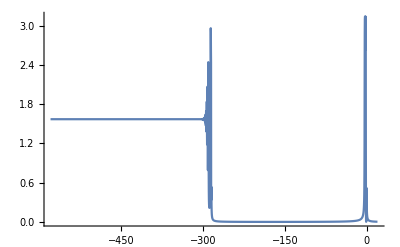

```mathematica
Plot[2β √Δ K1[z]/.parameters/.nsolKv,{z,-580,20},PlotRange->All]
```

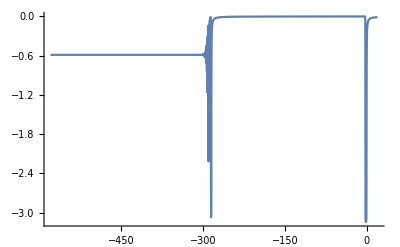

```mathematica
Plot[β √Δ K2[z]/.parameters/.nsolKv,{z,-580,20},PlotRange->All]
```

```mathematica
KretschmannN2=(Kretschmann/.{x-> t+z}/.chvarearly/.D[chvarearly, z]//Expand)/.parameters/.nsolKv/.D[nsolKv, z]/.D[D[nsolKv, z], z];
```

General::munfl: Exp[-719.652] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1443.47] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-721.733] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

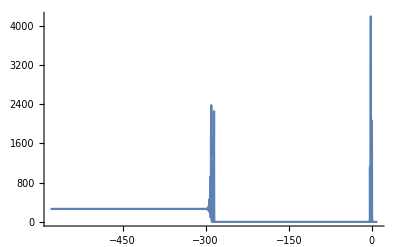

```mathematica
Plot[KretschmannN2,{z,-580,10},PlotRange->All]
```

```mathematica
diffC0=Eϕ[z]Kϕ'[z]-Ex'[z]Kx[z];
vector=(diffC0/(Eϕ[z] √Ex[z])/.chvarearly//Simplify)/.nsolKv/.D[nsolKv, z];
```

```mathematica
vector/.z-> -285.6000000002
```

2.13163×10^-14

```mathematica
Plot[vector/.z->x,{x,-295,-280},PlotRange->All]
```

$Aborted

```mathematica
error1/.z->-285.6000000002
```

1.88122×10^-10

```mathematica
error1=Norm[(eomKv//Simplify)//Expand]/.parameters/.nsolKv/.D[nsolKv, z];
```

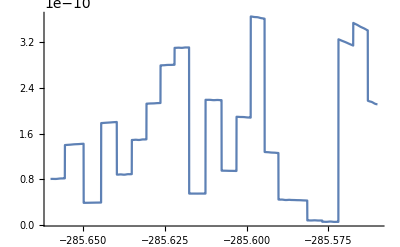

```mathematica
Plot[error1,{z,-285.66,-285.56},PlotRange->All]
```

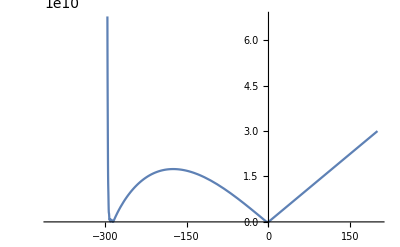

```mathematica
Plot[Eϕ[z] √Ex[z]/.chvarearly/.nsolKv,{z,-400,200}]
```

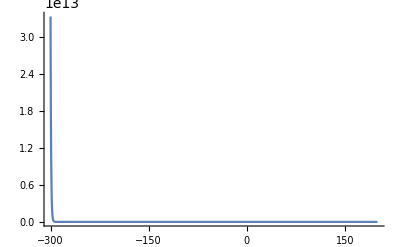

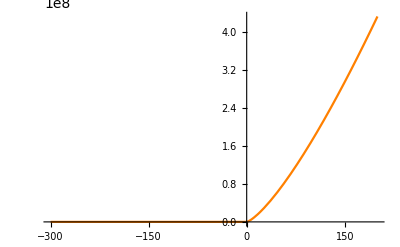

```mathematica
Plot[Eϕ[z]/.chvarearly/.nsolKv,{z,-300,200},PlotRange->All]
Plot[Ex[z]/.chvarearly/.nsolKv,{z,-300,200},PlotRange->All]
```

```mathematica
mid=-350;
```

```mathematica
newbdy={ K1[z1]->K1[z] , K2[z1]-> K2[z],Ex[z]->ⅇ^v1[z],Eϕ[z]->ⅇ^v2[z]}/.nsolKv/.z-> mid/.z1-> mid
```

{K1[-350]→2.48365,K2[-350]→-1.85699,Ex[-350]→0.124823,Eϕ[-350]→1.03157×10^39}

```mathematica
Log[1.031574611273325*^39]
```

89.8319

```mathematica
Log[0.12482261460952522]
```

-2.08086

```mathematica
bdyKu={K1[z]== K1[x0],K2[z]== K2[x0],u[z]==Log[Eϕ[x0]],Ex[z]== Ex[x0]}/.x0->mid/.newbdy/.z-> mid
```

{K1[-350]==2.48365,K2[-350]==-1.85699,u[-350]==89.8319,Ex[-350]==0.124823}

```mathematica
bdyKu1={K1[z]->  K1[x0],K2[z]->  K2[x0],Ex[z]->  Ex[x0]}/.x0->mid/.newbdy
```

{K1[z]→2.48365,K2[z]→-1.85699,Ex[z]→0.124823}

```mathematica
asymp=eomKEuasym/.{K1'[z]->0,K2'[z]->0}/.parameters/.bdyKu1
```

{1.86517×10^-14,-3.55271×10^-15,-1.23906×10^-16+Ex'[z],1.17395+u'[z]}

```mathematica
uns=DSolve[{asymp[[4]]==0,bdyKu[[3]]},u[z],z]//Expand//Flatten
```

{u[z]→-321.05-1.17395 z}

```mathematica
nsolutionODEKu={bdyKu1,uns,K1'[z]->0,K2'[z]->0,Ex'[z]->0,Ex''[z]->0}//Flatten
```

{K1[z]→2.48365,K2[z]→-1.85699,Ex[z]→0.124823,u[z]→-321.05-1.17395 z,K1'[z]→0,K2'[z]→0,Ex'[z]→0,Ex''[z]→0}

```mathematica
eomKEuasym/.nsolutionODEKu/.D[nsolutionODEKu, z]/.parameters
```

{1.77636×10^-14,-3.55271×10^-15,-1.23906×10^-16,0.}

```mathematica
(diffC0/.chvar//Simplify)
```

(ⅇ^u[z] (-2 K1[z] Ex'[z]+K2[z] Ex'[z]+2 Ex[z] K2'[z]))/(2 √Ex[z])

```mathematica
HmubarS*G/.x->z/.chvar/.parameters/.nsolutionODEKu//Expand
```

0.-6.66134×10^-16 ⅇ^(-321.05-1.17395 z)

```mathematica
neffeomODEKu={Table[eomKEuasym[[i]]==0,{i,1,3}],bdyKu}/.parameters//Flatten;
(*nsolutionODEKu1=NDSolve[neffeomODEKu,{K1[z],K2[z],Ex[z],u[z]},{z,-xM,-275},Method->"ImplicitRungeKutta"]//Flatten*)
KKEns=NDSolve[neffeomODEKu,{K1[z],K2[z],Ex[z]},{z,-xM,mid},Method-> {"StiffnessSwitching",Method->{"ExplicitRungeKutta",Automatic}},PrecisionGoal->14,AccuracyGoal->14]//Flatten;
uns=NDSolve[{(eomKEuasym[[4]]==0/.KKEns/.parameters),bdyKu},u[z],{z,-xM,mid},Method->"ImplicitRungeKutta",PrecisionGoal->14,AccuracyGoal->14];
nsolutionODEKu={KKEns,uns}//Flatten
```

{K1[z]→InterpolatingFunction[…][z],K2[z]→InterpolatingFunction[…][z],Ex[z]→InterpolatingFunction[…][z],u[z]→InterpolatingFunction[…][z]}

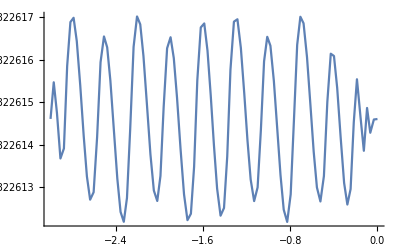

```mathematica
Plot[Ex[z]/.nsolutionODEKu,{z,-xM,mid},PlotRange->All]
```

General::munfl: Exp[-4350.42] is too small to represent as a normalized machine number; precision may be lost.

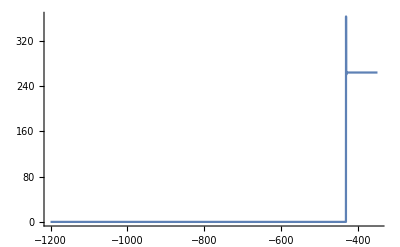

```mathematica
KretschmannN3=(Kretschmann/.{x-> t+z}/.chvar/.D[chvar, z]//Simplify)/.parameters/.nsolutionODEKu/.D[nsolutionODEKu, z]/.D[D[nsolutionODEKu, z], z];
Plot[KretschmannN3,{z,-1200,mid},PlotRange->All]
```

General::munfl: Exp[-7.04355×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.40871×10^9] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 8.01137 7.63727967979855×10^-305897391 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

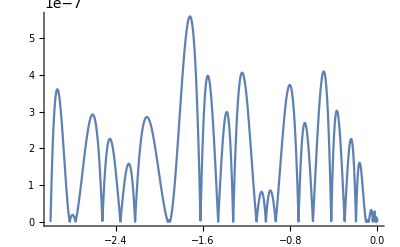

```mathematica
error2=Norm[eomKEu//Simplify]/.parameters/.nsolutionODEKu/.D[nsolutionODEKu, z];
Plot[error2,{z,-xM,mid},PlotRange->All]
```

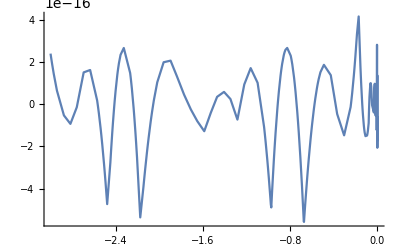

```mathematica
diffC0=Eϕ[z]Kϕ'[z]-Ex'[z]Kx[z];
Plot[(diffC0/(Eϕ[z] √Ex[z])/.chvar//Simplify)/.nsolutionODEKu/.D[nsolutionODEKu, z]/.z->x,{x,-xM,mid},PlotRange->All]
```

```mathematica
evalns[f_,x_]:=If[x⩾mid,((f/.chvarearly/.D[chvarearly, z]//Expand)/.nsolKv /.D[nsolKv, z]/.D[D[nsolKv, z], z])/.z->x,0]+If[x<mid,((f/.chvar/.D[chvar, z]//Expand)/.nsolutionODEKu /.D[nsolutionODEKu, z]/. D[D[nsolutionODEKu, z], z])/.z->x,0];
```

```mathematica
eval[f_,x_]:=Module[{f1=((Simplify[f/.chvarearly/.D[chvarearly, z]]//Expand)/.nsolKv /.D[nsolKv, z]/.D[D[nsolKv, z], z]),f2=((Simplify[f/.chvar/.D[chvar, z]]//Expand)/.nsolutionODEKu /.D[nsolutionODEKu, z]/. D[D[nsolutionODEKu, z], z])},If[N[x]⩾mid,f1/.z->x,f2/.z->x]];
```

```mathematica
eval1[f_,x_]:=UnitStep[x-mid]*((Simplify[f/.chvarearly/.D[chvarearly, z]]//Expand)/.nsolKv /.D[nsolKv, z]/.D[D[nsolKv, z], z]/.z->x)+UnitStep[-(x-mid)]*((Simplify[f/.chvar/.D[chvar, z]]//Expand)/.nsolutionODEKu /.D[nsolutionODEKu, z]/. D[D[nsolutionODEKu, z], z]/.z->x);
```

### Kretschmann scalar

```mathematica
evaluateKretschmann=eval1[Kretschmann/.x-> t+z,y];
```

General::munfl: Exp[-1470.96] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2941.93] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

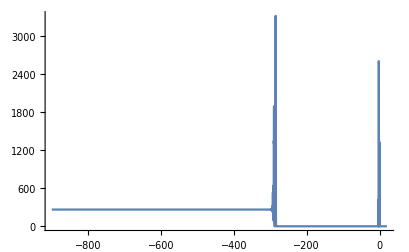

```mathematica
Plot[evaluateKretschmann,{y,-900,20},PlotRange->All]
```

### energy density and average null energy condition

```mathematica
CpullinS
```

-(2 π (16 Ex[x] Eϕ[x]^2 Kx[x] Kϕ[x]+4 Eϕ[x]^3 (1+Kϕ[x]^2)+4 Ex[x] Ex'[x] Eϕ'[x]-Eϕ[x] (Ex'[x]^2+4 Ex[x] Ex''[x])))/(κ √Ex[x] Eϕ[x]^2)

```mathematica
Λ=eval[Eϕ[z]/(√Ex[z]),y];
null1=NDSolve[{D[x[t], t]==1/(Λ/.y-> x[t]-t),x[0]==0},x[t],{t,-1000,1000}]
null2=NDSolve[{D[x[t], t]==-1/(Λ/.y-> x[t]-t),x[0]==0},x[t],{t,-1000,1000}]
```

{{x[t]→InterpolatingFunction[…][t]}}

{{x[t]→InterpolatingFunction[…][t]}}

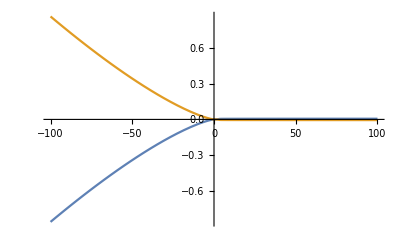

```mathematica
Plot[{x[t]/.null1[[1]],x[t]/.null2[[1]]},{t,-100,100},AxesOrigin->{0,0}]
```

```mathematica
U={1,(Eϕ[z]/(√Ex[z]))^-1,0,0};
V={1,-(Eϕ[z]/(√Ex[z]))^-1,0,0};
TUU0=(1/(8π)(∑_(i=1)^4 ∑_(j=1)^4 Einstein[[i,j]]U[[i]]U[[j]])/.x->t+z//Simplify)//Expand
TVV0=(1/(8π)(∑_(i=1)^4 ∑_(j=1)^4 Einstein[[i,j]]V[[i]]V[[j]])/.x->t+z//Simplify)//Expand
```

(Ex'[z] Eϕ'[z])/(8 π Eϕ[z]^3)-(Ex'[z] Eϕ'[z])/(4 π √Ex[z] Eϕ[z]^2)+(Ex'[z] Eϕ'[z])/(8 π Ex[z] Eϕ[z])-Ex''[z]/(8 π Ex[z])-Ex''[z]/(8 π Eϕ[z]^2)+Ex''[z]/(4 π √Ex[z] Eϕ[z])

(Ex'[z] Eϕ'[z])/(8 π Eϕ[z]^3)+(Ex'[z] Eϕ'[z])/(4 π √Ex[z] Eϕ[z]^2)+(Ex'[z] Eϕ'[z])/(8 π Ex[z] Eϕ[z])-Ex''[z]/(8 π Ex[z])-Ex''[z]/(8 π Eϕ[z]^2)-Ex''[z]/(4 π √Ex[z] Eϕ[z])

```mathematica
TUU=(eval1[TUU0,z]/.{z->( x[t]/.null1[[1]])-t});
TVV=(eval1[TUU0,z]/.{z->( x[t]/.null1[[1]])-t});
```

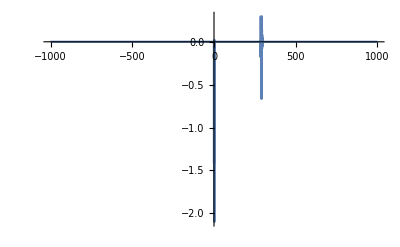

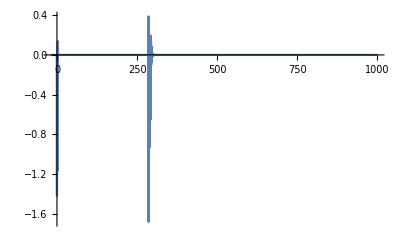

```mathematica
Plot[TUU,{t,-1000,1000},PlotRange->All]
Plot[TVV,{t,-20,1000},PlotRange->All,AxesOrigin->{0,0}]
```

```mathematica
NIntegrate [TUU,{t,-1000,1000}]
NIntegrate [TVV,{t,-1000,1000}]
```

-2.29749

-2.29749

### Metric conponents

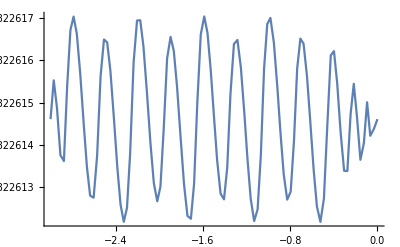

```mathematica
Plot[Ex[z]/.nsolutionODEKu,{z,-xM,mid},PlotRange->All,AxesOrigin->{mid,0}]
```

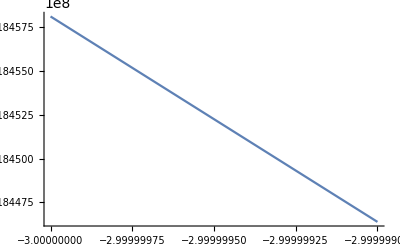

```mathematica
Λ=Eϕ[z]/(√Ex[z])/.chvar/.nsolutionODEKu ;
Plot[Log[Λ],{z,-xM,-xM+100},PlotRange->All]
```

```mathematica
Log[Λ]//Simplify
```

-320.01-1.17395 z

```mathematica
model=LinearModelFit[Transpose[{Table[0.1i,{i,1,100}],Table[Log[Λ]/.z-> -xM+10-0.1i,{i,1,100}]}],x,x]
```

FittedModel[3.52185×10^8+1.17395 x]

```mathematica
lnΛ[z]=(Normal[model]/.x-> -xM+10-z//Expand)
```

-298.903-1.17395 z

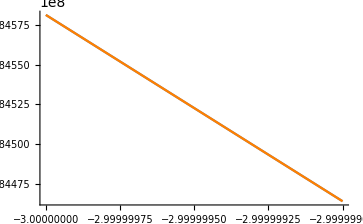

```mathematica
Show[Plot[Log[Λ],{z,-xM,-xM+100},PlotRange->All],Plot[lnΛ[z],{z,-xM,-xM+100},PlotRange->All,PlotStyle-> Orange]]
```

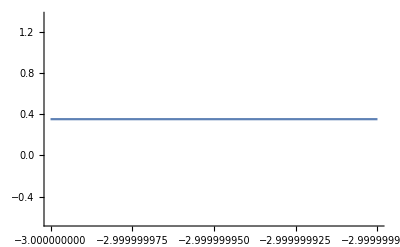

```mathematica
R=√Ex[z];
Plot[eval[R,x],{x,-xM,-xM+10},PlotRange->All]
```

```mathematica
√Ex[z]/.nsolutionODEKu/.z-> -xM
```

0.353302

```mathematica
eval[√Ex[z],-xM]
```

0.353302

```mathematica
K1[z]/.nsolutionODEKu/.z-> -xM
```

2.48365

```mathematica
K2[z]/.nsolutionODEKu/.z-> -xM
```

-1.85699

```mathematica
u[z]/.nsolutionODEKu/.z-> -xM
```

3.52185×10^8

```mathematica
nsolutionODEKu
```

{K1[z]→2.48365,K2[z]→-1.85699,Ex[z]→0.124823,u[z]→-321.05-1.17395 z}

```mathematica
u[z]/.nsolutionODEKu/.z->-xM
```

3.52185×10^8

## de Sitter X S^2

```mathematica
L[z_]-> ⅇ^lnΛ[z]
```

L[z_]→ⅇ^(-371.252-1.17395 z)

```mathematica
(* near horizon metric *)
q={{-1,0},{0,L[x-t]^2}};
```

```mathematica
d=2;
xx={t,x};
```

```mathematica
qinv=FullSimplify[Inverse[q],Assumptions->{r>0}]
```

{{-1,0},{0,1/L[-t+x]^2}}

```mathematica
Christ = ParallelTable[Simplify[∑_(ρ=1)^d 1/2 qinv[[σ,ρ]](D[q[[ρ,μ]], xx[[ν]]]+D[q[[ρ,ν]], xx[[μ]]]-D[q[[μ,ν]], xx[[ρ]]]),Assumptions->{Rs>0}] , {σ, 1, d}, {μ, 1, d}, {ν, 1, d}];
```

```mathematica
Rie = ParallelTable[Simplify[-D[Christ[[σ,ν,ρ]], xx[[μ]]] + D[Christ[[σ,μ,ρ]], xx[[ν]]] + ∑_(λ=1)^d (Christ[[λ,ρ,μ]]Christ[[σ,ν,λ]]-Christ[[λ,ρ,ν]]Christ[[σ,μ,λ]]),Assumptions->{Rs>0}] , {μ, 1,d}, {ν, 1, d}, {ρ, 1, d}, {σ, 1, d}];
```

```mathematica
Ricci = ParallelTable[Simplify[∑_(ν=1)^d Rie[[μ,ν,ρ,ν]] ,Assumptions->{Rs>0}], {μ, 1, d}, {ρ, 1, d}];
RicciScalar = ∑_(a=1)^d ∑_(b=1)^d qinv[[a,b]]Ricci[[a,b]] ;
```

```mathematica
√(RicciScalar/2)
```

√(L''[-t+x]/L[-t+x])

```mathematica
invradius=(√(RicciScalar/2))/.{L[z_]-> ⅇ^lnΛ[z],L''[z_]-> D[D[ⅇ^lnΛ[z], z], z]}
```

1.17395

```mathematica
{L[z_]-> ⅇ^lnΛ[z],L''[z_]-> D[D[ⅇ^lnΛ[z], z], z]}
```

{L[z_]→ⅇ^(-371.252-1.17395 z),L''[z_]→1.37816 ⅇ^(-371.252-1.17395 z)}

```mathematica
Ricci -invradius^2 q/.{L[z_]-> ⅇ^lnΛ[z],L''[z_]-> D[D[ⅇ^lnΛ[z], z], z]}
```

{{0.,0.},{0.,0.}}

```mathematica
Table[∑_(α=1)^2 q[[α,σ]]Rie[[μ,ν,ρ,α]]-invradius^2*(q[[μ,ρ]]q[[ν,σ]]-q[[ν,ρ]]q[[μ,σ]]),{μ, 1,d}, {ν, 1, d}, {ρ, 1, d}, {σ, 1, d}]/.{L[z_]-> ⅇ^lnΛ[z],L''[z_]-> D[D[ⅇ^lnΛ[z], z], z]}
```

{{{{0.,0.},{0.,0.}},{{0.,0.},{0.,0.}}},{{{0.,0.},{0.,0.}},{{0.,0.},{0.,0.}}}}

```mathematica
Q->(√(rb^2-invradius^2 rb^4))/(√2)/.rb-> eval[√Ex[z],-xM]
```

Q→0.227321

```mathematica
M->1/3 (2 rb-invradius^2 rb^3)/.rb-> eval[√Ex[z],-xM]
```

M→0.215276

## Classical limit of effective EOM

```mathematica
effeom0=Series[effeom,{Δ,0,0}]//Normal//Expand
```

{Kx^(1,0)[t,x]==Eϕ[t,x]/(4 Ex[t,x]^(3/2))-(Kx[t,x] Kϕ[t,x])/(√Ex[t,x])+(Eϕ[t,x] Kϕ[t,x]^2)/(4 Ex[t,x]^(3/2))-((Ex^(0,1)[t,x])^2)/(16 Ex[t,x]^(3/2) Eϕ[t,x])-(Ex^(0,1)[t,x] Eϕ^(0,1)[t,x])/(4 √Ex[t,x] Eϕ[t,x]^2)+(Ex^(0,2)[t,x])/(4 √Ex[t,x] Eϕ[t,x]),Kϕ^(1,0)[t,x]==-1/(2 √Ex[t,x])-Kϕ[t,x]^2/(2 √Ex[t,x])+((Ex^(0,1)[t,x])^2)/(8 √Ex[t,x] Eϕ[t,x]^2),Ex^(1,0)[t,x]==2 √Ex[t,x] Kϕ[t,x],Eϕ^(1,0)[t,x]==2 √Ex[t,x] Kx[t,x]+(Eϕ[t,x] Kϕ[t,x])/(√Ex[t,x])}

```mathematica
solK00=Solve[{effeom0[[3]],effeom0[[4]]},{Kx[t,x],Kϕ[t,x]}];
solK0=Flatten[{solK00,D[solK00, t]}];
```

```mathematica
sndeom0=({effeom0[[1]],effeom0[[2]]}/.solK0//FullSimplify)//Expand
({effeom0[[3]],effeom0[[4]]}/.solK0//FullSimplify)//Expand
```

{-4 √Ex[t,x] Eϕ[t,x]^2+√Ex[t,x] (Ex^(0,1)[t,x])^2+(4 Ex[t,x]^(3/2) Ex^(0,1)[t,x] Eϕ^(0,1)[t,x])/Eϕ[t,x]-4 Ex[t,x]^(3/2) Ex^(0,2)[t,x]+(3 Eϕ[t,x]^2 (Ex^(1,0)[t,x])^2)/(√Ex[t,x])-4 √Ex[t,x] Eϕ[t,x] Ex^(1,0)[t,x] Eϕ^(1,0)[t,x]-4 √Ex[t,x] Eϕ[t,x]^2 Ex^(2,0)[t,x]+8 Ex[t,x]^(3/2) Eϕ[t,x] Eϕ^(2,0)[t,x]==0,4 √Ex[t,x] Eϕ[t,x]-(√Ex[t,x] (Ex^(0,1)[t,x])^2)/Eϕ[t,x]-(Eϕ[t,x] (Ex^(1,0)[t,x])^2)/(√Ex[t,x])+4 √Ex[t,x] Eϕ[t,x] Ex^(2,0)[t,x]==0}

{True,True}

```mathematica
BLTmetric={{(D[R[t,x], x])^2/(1+E0[x]),0,0},{0,R[t,x]^2,0},{0,0,R[t,x]^2 Sin[θ]^2}};
BLTcotriad={{D[R[t,x], x]/(√(1+E0[x])),0,0},{0, R[t,x],0},{0,0, R[t,x]Sin[θ]}};
BLTdtriad=FullSimplify[√Det[BLTmetric] Inverse[BLTcotriad]//FullSimplify,Assumptions->{D[R[t,x], x]>0,R[t,x]>0,Sin[θ]>0,u>0,v>0}]
```

{{R[t,x]^2 Sin[θ],0,0},{0,(R[t,x] Sin[θ] R^(0,1)[t,x])/(√(1+E0[x])),0},{0,0,(R[t,x] R^(0,1)[t,x])/(√(1+E0[x]))}}

```mathematica
ansatz00={Ex[t_,x_]->BLTdtriad[[1,1]]/Sin[θ], Eϕ[t_,x_]->BLTdtriad[[3,3]] };
ansatz0=Flatten[{ansatz00,{Derivative[1,0][Ex][t_,x_]->D[(BLTdtriad[[1,1]]/Sin[θ]), t], Derivative[1,0][Eϕ][t_,x_]->D[BLTdtriad[[3,3]], t] },{Derivative[0,1][Ex][t_,x_]->D[(BLTdtriad[[1,1]]/Sin[θ]), x], Derivative[0,1][Eϕ][t_,x_]->D[BLTdtriad[[3,3]], x] },{Derivative[2,0][Ex][t_,x_]->D[D[(BLTdtriad[[1,1]]/Sin[θ]), t], t], Derivative[2,0][Eϕ][t_,x_]->D[D[BLTdtriad[[3,3]], t], t] },{Derivative[0,2][Ex][t_,x_]->D[D[(BLTdtriad[[1,1]]/Sin[θ]), x], x], Derivative[0,2][Eϕ][t_,x_]->D[D[BLTdtriad[[3,3]], x], x] }}]//FullSimplify;
```

```mathematica
soltest0={D[R[t,x], t]->  s √(E0[x]+F0[x]/R[t,x])};
soltest=Flatten[{soltest0,D[soltest0, t],D[D[soltest0, t], t],D[D[soltest0, x], t],D[soltest0, x]}]//FullSimplify;
```

```mathematica
eom0reduce=(Refine[sndeom0/.ansatz0,Assumptions->{R[t,x]>0}]/.soltest//Expand)/.soltest/.s^2-> 1//FullSimplify
```

{True,True}

```mathematica
ansatz00
solK00
```

{Ex[t_,x_]→R[t,x]^2,Eϕ[t_,x_]→(R[t,x] R^(0,1)[t,x])/(√(1+E0[x]))}

{{Kx[t,x]→-(Eϕ[t,x] Ex^(1,0)[t,x]-2 Ex[t,x] Eϕ^(1,0)[t,x])/(4 Ex[t,x]^(3/2)),Kϕ[t,x]→(Ex^(1,0)[t,x])/(2 √Ex[t,x])}}

```mathematica
Clear[R]
```

```mathematica
sol0thorder={Ex[t,x]->R[t,x]^2,Eϕ[t,x]->(R[t,x] Derivative[0,1][R][t,x])/(√(1+E0[x])),FullSimplify[solK00/.Flatten[{Ex[t,x]->R[t,x]^2,Eϕ[t,x]->(R[t,x] Derivative[0,1][R][t,x])/(√(1+E0[x])),D[Ex[t,x], t]->D[(R[t,x]^2), t],D[Eϕ[t,x], t]->D[((R[t,x] Derivative[0,1][R][t,x])/(√(1+E0[x]))), t]}],Assumptions->{R[t,x]>0}]}//Flatten
```

{Ex[t,x]→R[t,x]^2,Eϕ[t,x]→(R[t,x] R^(0,1)[t,x])/(√(1+E0[x])),Kx[t,x]→(R^(1,1)[t,x])/(2 √(1+E0[x])),Kϕ[t,x]→R^(1,0)[t,x]}

```mathematica
schwarz=sol0thorder/.{E0[x]->0,E0'[x]->0,F0[x]-> Rs,F0'[x]->0,R[t,x]-> (3/2 √Rs(x-t))^(2/3),D[R[t,x], x]-> D[((3/2 √Rs(x-t))^(2/3)), x],D[D[R[t,x], t], x]->D[D[((3/2 √Rs(x-t))^(2/3)), t], x],D[R[t,x], t]-> D[((3/2 √Rs(x-t))^(2/3)), t]}//Simplify
```

{Ex[t,x]→3/2 (3/2)^(1/3) (√Rs (-t+x))^(4/3),Eϕ[t,x]→(3/2)^(1/3) √Rs (√Rs (-t+x))^(1/3),Kx[t,x]→Rs/(3 2^(2/3) 3^(1/3) (√Rs (-t+x))^(4/3)),Kϕ[t,x]→-((2/3)^(1/3) √Rs)/(√Rs (-t+x))^(1/3)}

```mathematica
FullSimplify[sol0thorder/.{E0[x]->0,E0'[x]->0,F0[x]-> Rs[x],F0'[x]->Rs'[x],R[t,x]-> (3/2 √Rs[x](x-t))^(2/3),D[R[t,x], x]-> D[((3/2 √Rs[x](x-t))^(2/3)), x],D[D[R[t,x], t], x]->D[D[((3/2 √Rs[x](x-t))^(2/3)), t], x],D[R[t,x], t]-> D[((3/2 √Rs[x](x-t))^(2/3)), t]}//FullSimplify,Assumptions-> {x>t, Rs[x]>0}]
```

{Ex[t,x]→3/2 (3/2)^(1/3) (-t+x)^(4/3) Rs[x]^(2/3),Eϕ[t,x]→1/2 (3/2)^(1/3) ((-t+x)/Rs[x])^(1/3) (2 Rs[x]+(-t+x) Rs'[x]),Kx[t,x]→(Rs[x]+(t-x) Rs'[x])/(3 2^(2/3) 3^(1/3) ((t-x)^2 Rs[x])^(2/3)),Kϕ[t,x]→-(2/3)^(1/3) (Rs[x]/(-t+x))^(1/3)}